## Essential code

### SSS & Causal Network Construction

Build a causal network from a SSS, modeling the Sequential Substituion System using tags.  This allows us to build the SSS evolution and the causal network simultaneously.  
(Based on code from NKS, pp. 1033, and suggestions of Matthew Szudzik.)

#### Format conversion

```mathematica
Attributes[s]=Flat;
```

```mathematica
Clear[SSSConvert];
SSSConvert[string_String] := s@@(Characters[string]/.Thread[CharacterRange["A","Z"]->Range[0,25]])
SSSConvert[s[x__]] := StringJoin[{x}/.Thread[Range[0,25]->CharacterRange["A","Z"]]]
```

```mathematica
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats.";
```

```mathematica
?SSSConvert
```

Converts SSS (sequential substitution system) states between s- and string-formats.

```mathematica
SSSConvert["AABBBA"]
```

s[0,0,1,1,1,0]

```mathematica
SSSConvert[%]
```

AABBBA

#### SSSRuleIcon

```mathematica
$MaxColor=6;  (* If you want to treat SSSs with more than 6 symbols, just change this variable *)
```

```mathematica
myColors=Sequence[ColorRules->{0->LightGray},ColorFunction->(Hue[(#-1)/$MaxColor]&),ColorFunctionScaling->False];
```

```mathematica
patternPrint[pattern_,opts___] := ArrayPlot[{{##}}& @@pattern,myColors,Mesh->True,opts,ImageSize->{Automatic,20}];
```

```mathematica
Clear[SSSRuleIcon];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,opts___] := Panel[Grid[Map[patternPrint[#,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
```

```mathematica
SSSRuleIcon::usage="SSSRuleIcon[rule(s)] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```

```mathematica
?SSSRuleIcon
```

SSSRuleIcon[
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"]] generates an icon for a sequential substitution system (SSS) rule or set of rules.


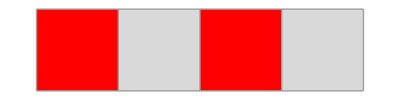
-Graphics- | → | -Graphics-Substitution Rule:

```mathematica
SSSRuleIcon["ABA"->"BABA"]
```

#### Initialization

Since we're going to have to initialize the global variables $SSSConnectionList and $SSSTagIndex anyway, let's add another: $SSSInitial

```mathematica
Clear[SSSInitialize];
SSSInitialize[string_String,mode___] := (
$SSSInitial=s@@Transpose[{#,Range[Length[#]]}& @ (Characters[string]/.Thread[CharacterRange["A","Z"]->Range[0,25]])];
$SSSConnectionList={}; 
$SSSTagIndex=StringLength[string]+1;                     (* value of next tag to use *)
If[mode=!=Quiet,Print["SSS Initialized."]];)
```

```mathematica
SSSInitialize::usage = "SSSInitialize[string] performs the necessary initializion step to generate sequential substitution system (SSS) evolutions and networks, starting with an initial SSS state string, e.g., \"BABA\". 

SSSInitialize[string, Quiet] performs the initialization but suppresses the success message.

(The tagged SS form of the initial state is stored in $SSSInitial and the values of $SSSConnectionList and $SSSTagIndex are reset by this operation.)";
```

```mathematica
?SSSInitialize
```

SSSInitialize[
StyleBox["string",
FontSlant->"Italic"]] performs the necessary initializion step to generate sequential substitution system (SSS) evolutions and networks, starting with an initial SSS state 
StyleBox["string",
FontSlant->"Italic"], e.g., "BABA". 

SSSInitialize[
StyleBox["string",
FontSlant->"Italic"], Quiet] performs the initialization but suppresses the success message.

(The tagged SS form of the initial state is stored in $SSSInitial and the values of $SSSConnectionList and $SSSTagIndex are reset by this operation.)

```mathematica
SSSInitialize["BABA",Quiet]
```

```mathematica
$SSSInitial
```

s[{1,1},{0,2},{1,3},{0,4}]

```mathematica
SSSInitialize["BABA"];  $SSSInitial
```

SSS Initialized.

s[{1,1},{0,2},{1,3},{0,4}]

#### Format conversion

I think I only need a one-way conversion, at least for the moment, but for visualization, here's a convert/strip function to strip out tags and recover the String notation:

```mathematica
SSSStrip[s[x__]] := StringJoin[First /@ {x}/.Thread[Range[0,25]->CharacterRange["A","Z"]]];
SSSStrip[s[]]="";
```

```mathematica
SSSStrip::usage="SSSStrip[state] strips out tags from a state given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
?SSSStrip
```

SSSStrip[
StyleBox["state",
FontSlant->"Italic"]] strips out tags from a 
StyleBox["state",
FontSlant->"Italic"] given in tagged SSS (sequential substitution system) format and returns it in string format.

#### Single step

```mathematica
SSSSingleStep[rules_,state___] := If[state===Null,$SSSInitial,state] /. rules
```

But we can't use it until we have a convenient way to convert old style rules to new style rules.  For example, s[1,0]→s[0,1,0] should be rewritten as

s[{1, a_}, {0, b_}] :> (AppendTo[$SSSConnectionList, {a, b} → $SSSTagIndex + {0, 1, 2}];  s[{0, $SSSTagIndex++}, {1, $SSSTagIndex++}, {0, $SSSTagIndex++}])

```mathematica
SSSSingleStep::usage="SSSSingleStep[rules,state] performs a single step of the sequential substitution system (SSS) evolution, applying the SSS rules (which must be generated by SSSNewRule) to the specified state. This operation updates the global variables $SSSConnectionList and $SSSTagIndex.";
```

```mathematica
SSSInitialize["ABBA"]
```

SSS Initialized.

```mathematica
$SSSInitial
```

s[{0,1},{1,2},{1,3},{0,4}]

```mathematica
SSSNewRule["AB"->"BA"]
```

s[{0,lhsTag$973245_},{1,lhsTag$973246_}]:>(AppendTo[$SSSConnectionList,{lhsTag$973245,lhsTag$973246}→$SSSTagIndex+{0,1}];s@@{{1,$SSSTagIndex++},{0,$SSSTagIndex++}})

```mathematica
SSSSingleStep[SSSNewRule["AB"->"BA"],$SSSInitial]
```

s[{1,5},{0,6},{1,3},{0,4}]

#### Generate a rule for the tagged SSS

```mathematica
SSSNewRule[rule_Rule | rule_RuleDelayed] := Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@ Transpose@{Characters[lhs]/.
Thread[CharacterRange["A","Z"]->Range[0,25]] ,ToString@#<>"_"& /@ lhsNames}];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2="s@@"<>ToString[("{"<>ToString@#<>
", $SSSTagIndex++}")& /@ (Characters[rhs]/.Thread[CharacterRange["A","Z"]->Range[0,25]] )];
ToExpression[newlhs<>" :> ("<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := SSSNewRule/@rules
```

```mathematica
SSSNewRule::usage="SSSNewRule[rule(s)] generates the needed rule(s) for the tagged SSS (sequential substitution system) from the rule(s) given in string-format: e.g., \"BA\"→\"ABA\"";
```

#### SSSEvolve

And finally the evolve function.  Note!  Although SSSSingleStep expected a new format rule, for convenience and efficiency the evolve function will take an String-format rule and do the conversion once.  It will also be assumed to operate on $SSSInitial.  Again, since some global functions were unavoidable, we'll save the rulelist and the complete evolution in global variables $SSSRules and $SSSEvolution:

```mathematica
SSSEvolve[rules_, n_Integer] := ($SSSEvolution=Module[{convertedrules=SSSNewRule[$SSSRules=rules]},
NestList[SSSSingleStep[convertedrules,#]&,$SSSInitial,n]])
```

```mathematica
SSSEvolve::usage="SSSEvolve[rule(s), n] generates n levels of the tagged SSS (sequential substitution system) using rules(s). The initial state must have been previously set by SSSInitialize[initialstate] or SSSInitialize[initialstate,Quiet].  

(The result is returned, but is also available in the global variable $SSSEvolution.  The global variables $SSSRules and $SSSConnectionList are set equal to the set of rules (in simple string form) and the updated causal network connection list, respectively.)";
```

```mathematica
?SSSEvolve
```

SSSEvolve[
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"], 
StyleBox["n",
FontSlant->"Italic"]] generates 
StyleBox["n",
FontSlant->"Italic"] levels of the 
StyleBox["tagged",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["SSS",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"](sequential substitution system) using 
StyleBox["rules",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"]. The initial state must have been previously set by SSSInitialize[
StyleBox["initialstate",
FontSlant->"Italic"]] or SSSInitialize[
StyleBox["initialstate",
FontSlant->"Italic"],Quiet].  

(The result is returned, but is also available in the global variable $SSSEvolution.  The global variables $SSSRules and $SSSConnectionList are set equal to the set of rules (in simple string form) and the updated causal network connection list, respectively.)

```mathematica
SSSInitialize["BABA"];
SSSEvolve["BA"->"ABA",5];
$SSSEvolution//Column
```

SSS Initialized.

s[{1,1},{0,2},{1,3},{0,4}]
s[{0,5},{1,6},{0,7},{1,3},{0,4}]
s[{0,5},{0,8},{1,9},{0,10},{1,3},{0,4}]
s[{0,5},{0,8},{0,11},{1,12},{0,13},{1,3},{0,4}]
s[{0,5},{0,8},{0,11},{0,14},{1,15},{0,16},{1,3},{0,4}]
s[{0,5},{0,8},{0,11},{0,14},{0,17},{1,18},{0,19},{1,3},{0,4}]

```mathematica
SSSStrip /@ $SSSEvolution
```

{BABA,ABABA,AABABA,AAABABA,AAAABABA,AAAAABABA}

#### SSSMakeNet

Time to make the donuts -- Ahem! -- ... to make the causal network from the SSS.  Oh, wait, we've already made an event list of the type described on p.1033 of the NKS book.  Now to use the code given there for converting an event list into a causal network:

```mathematica
SSSMakeNet := ($SSSNet=
With[{u=Map[First,$SSSConnectionList]},
Cases[
Flatten[Thread /@ #]& @
MapIndexed[Function[{e,i},First[i]->((If[#==={},Infinity,#[[1,1]]]&[Position[u,#]])&/@Last[e])],$SSSConnectionList],
_?(FreeQ[#,∞]&)]]);
```

```mathematica
SSSMakeNet::usage="SSSMakeNet generates a causal network for the current SSS (sequential substitution system).

(Uses information from the connection list found in the global variable $SSSConnectionList. The result is returned, but is also available in the global variable $SSSNet.)";
```

```mathematica
?SSSMakeNet
```

SSSMakeNet generates a causal network for the current SSS (sequential substitution system).

(Uses information from the connection list found in the global variable $SSSConnectionList. The result is returned, but is also available in the global variable $SSSNet.)

```mathematica
SSSMakeNet
```

{1→2,1→2,2→3,2→3,3→4,3→4,4→5,4→5}

#### SSSDisplay

```mathematica
cellsDeleted[{l1_,l2_}] := Flatten[Position[l1,_?(!MemberQ[l2,#]& ),{1},Heads->False] ]
```

```mathematica
Clear[SSSDisplay]
```

```mathematica
Options[SSSDisplay]={HighlightMethod->True,ShowRule->Bottom,Mesh->True,
NetSize->{Automatic,500},SSSSize->{Automatic,500},IconSize->{Automatic,20},ImageSize->{Automatic,500},NetMethod->GraphPlot,Max->∞,SSSMax->Automatic,NetMax->Automatic, Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
```

```mathematica
SSSDisplay[opts:OptionsPattern[]] := Module[{HlM,SR,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,ev,net},
HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
SR=OptionValue[ShowRule];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
mx=OptionValue[Max];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];
ev=$SSSEvolution⟦1;;Min[sssmx,Length[$SSSEvolution]]⟧;
net=Select[$SSSNet,And@@Thread[List@@#<netmx]&];
doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];
cellsToHighlight=Flatten[#,2]&@MapIndexed[Outer[List,#1,#2]&,Reverse[cellsDeleted /@ Partition[ev,2,1]]];
rulesApplied=Reverse@MapIndexed[SSSStrip@ev[[First@#2,#1]]&,cellsDeleted /@ Partition[ev,2,1]] /. MapIndexed[First@#1->First@#2&,Flatten[{$SSSRules}]];
ans = 
ArrayPlot[Map[First,ev,{2}] /. s->List,myColors,Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied[[y]],{x,y}+.5{-1,1}}),
_,{}]];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[SR,
Right, Row[{ans," ",SSSRuleIcon[$SSSRules,ImageSize->IcS]}],
Left, Row[{SSSRuleIcon[$SSSRules,ImageSize->IcS]," ",ans}], 
Bottom|True, Column[{ans," ",SSSRuleIcon[$SSSRules,ImageSize->IcS]}], 
Top,  Column[{SSSRuleIcon[$SSSRules,ImageSize->IcS]," ",ans}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],VertexLabeling->True}]],{}],
If[doLGP,LayeredGraphPlot[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexLabeling->True}]],{}],
If[doTP,TreePlot[net,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexLabeling->True,DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexLabeling->True}]],{}]
},"  "]]
```

```mathematica
SSSDisplay::usage="SSSDisplay[opts] displays the current SSS (sequential substitution system) and/or SSS causal network, typically after a call to SSS (or to SSSInitialize, SSSEvolve and SSSMakeNet).

Options:
\tMax → n only shows the first n steps of the system.  (Separate values can be specified for SSSMax and NetMax.)

\tHighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

\tShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

\tSizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

\tNetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, where NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.  

(This function uses data stored in the global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSSDisplay
```

SSSDisplay[
StyleBox["opts",
FontSlant->"Italic"]] displays the current SSS (sequential substitution system) and/or SSS causal network, typically after a call to SSS (or to SSSInitialize, SSSEvolve and SSSMakeNet).

Options:
	Max → 
StyleBox["n",
FontSlant->"Italic"] only shows the first 
StyleBox["n",
FontSlant->"Italic"] steps of the system.  (Separate values can be specified for SSSMax and NetMax.)

	HighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

	ShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

	Sizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

	NetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, where NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.  

(This function uses data stored in the global variables $SSSRules, $SSSEvolution and $SSSNet.)

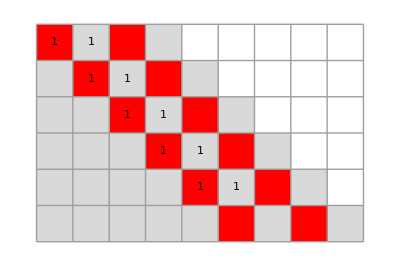

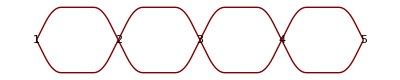
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSSDisplay[]
```

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->None,ImageSize->{Automatic,100},SSSSize->{Automatic,70}]
```

-Graphics- | → | -Graphics-Substitution Rule: -Graphics-

OptionValue::nodef: Unknown option GraphSize for SSSDisplay.

General::stop: Further output of OptionValue will be suppressed during this calculation.

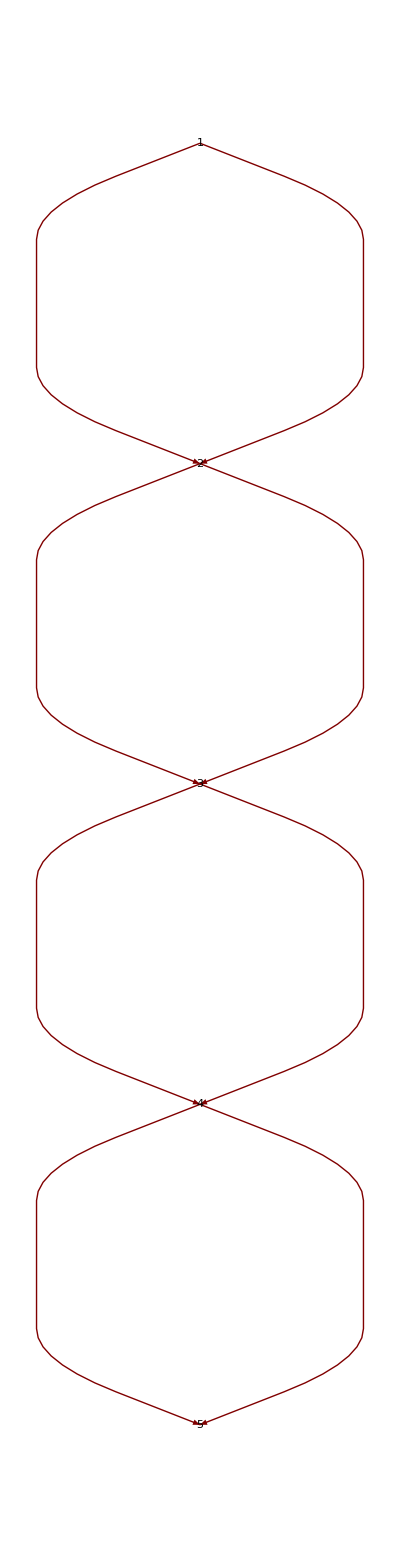
-Graphics- | → | -Graphics-Substitution Rule: -Graphics--Graphics-

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->TreePlot,SSSSize->{Automatic,300},ImageSize->{Automatic,300},GraphSize->{Automatic,300}]
```

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->{},SSSSize->{Automatic,300},ImageSize->{Automatic,300},GraphSize->{Automatic,300}]
```

OptionValue::nodef: Unknown option GraphSize for SSSDisplay.

General::stop: Further output of OptionValue will be suppressed during this calculation.

-Graphics- | → | -Graphics-Substitution Rule: -Graphics-

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->None]
```

-Graphics- | → | -Graphics-Substitution Rule: -Graphics-

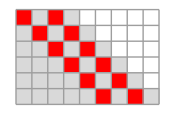
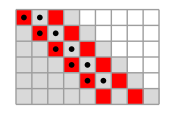
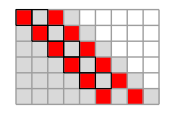
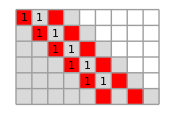
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

```mathematica
Row[SSSDisplay[HighlightMethod->#,NetMethod->None,ImageSize->175,SSSSize->175]& /@ {None,Dot,Frame,Number}]
```

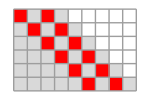
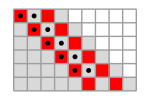
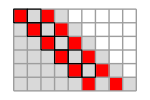
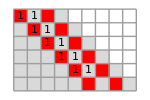
-Graphics- | → | -Graphics-Substitution Rule:-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Flatten@{
SSSRuleIcon[$SSSRules,ImageSize->{Automatic,15}],
SSSDisplay[HighlightMethod->#,ShowRule->None,NetMethod->None,ImageSize->150,SSSSize->150]& 
/@ {None,Dot,Frame,Number}}]
```

OptionValue::nodef: Unknown option GraphSize for SSSDisplay.

General::stop: Further output of OptionValue will be suppressed during this calculation.

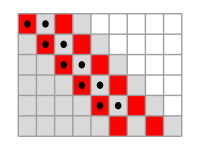
-Graphics- | → | -Graphics-Substitution Rule:
 
-Graphics--Graphics-

```mathematica
SSSDisplay[HighlightMethod->Dot,ShowRule->Top,SSSSize->{200,150},ImageSize->{200,200},NetMethod->GraphPlot,GraphSize->500]
```

OptionValue::nodef: Unknown option GraphSize for SSSDisplay.

General::stop: Further output of OptionValue will be suppressed during this calculation.

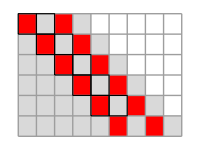
-Graphics- | → | -Graphics-Substitution Rule:
 
-Graphics--Graphics-

```mathematica
SSSDisplay[HighlightMethod->Frame,ShowRule->Top,SSSSize->{200,150},ImageSize->{200,200},NetMethod->GraphPlot,GraphSize->500]
```

#### SSS

The default workhorse function to build and display SSSs and their causal networks.  (After use, they can be used and redisplayed without rebuilding, using SSSDisplay, etc.)

```mathematica
SSS[rule_,init_,n_Integer,opts___] := (SSSInitialize[init,Quiet]; SSSEvolve[rule,n]; SSSMakeNet; SSSDisplay[opts])
```

```mathematica
SSS::usage="creates and displays a sequential substitution system (SSS) and its causal network. (After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
SSS::usage="SSS[rule(s), init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using rule(s) starting with the state init (using string notation), allowing the SSS to evolve for n steps.  
Any options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSS
```

SSS[
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["init",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["n",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["opts",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]creates and displays a sequential substitution system (SSS) and its causal network, using 
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"] starting with the state 
StyleBox["init",
FontSlant->"Italic"] (using string notation), allowing the SSS to evolve for 
StyleBox["n",
FontSlant->"Italic"] steps.  
Any options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRules, $SSSEvolution and $SSSNet.)

#### SSSAnimate

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
SSSAnimate := Module[{v},
Manipulate[
v=Sort@Thread[VertexList[ $SSSNet]->(VertexCoordinateRules /. Cases[graphtype[$SSSNet], _Rule, Infinity])];
SSSDisplay[HighlightMethod->highlight,ShowRule->Top, ImageSize->{250,485},SSSSize->{200,465},GraphSize->{600,485},Max->n,NetMethod->graphtype,VertexLabeling->vertexlabels,VertexCoordinateRules->v⟦;;n-1⟧,
Method->
Switch[graphtype,TreePlot,Automatic,LayeredGraphPlot,Automatic,_,"SpringElectricalEmbedding"]],
{n,3,Length[$SSSEvolution],1,Appearance->"Labeled"},{highlight,{Number,Dot,Frame,None}},{graphtype,{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D}},{vertexlabels,{True,False,Tooltip,All,Automatic}} ] ];
```

```mathematica
SSSAnimate::usage="SSSAnimate produces a manipulatable display of the current SSS (sequential substitution system) and its causal network, allowing the user to see the system evolve step by step and giving easy access to various display parameters.

(This function calls SSSDisplay and uses the information in global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSSAnimate
```

SSSAnimate produces a manipulatable display of the current SSS (sequential substitution system) and its causal network, allowing the user to see the system evolve step by step and giving easy access to various display parameters.

(This function calls SSSDisplay and uses the information in global variables $SSSRules, $SSSEvolution and $SSSNet.)

#### SSSPut/Get

```mathematica
SSSPut[fname_:"SSS"]:=({$SSSRules,$SSSEvolution,$SSSNet}>>Evaluate@DateString[{"SSS.","Year",".","Month",".","DayShort",".","Hour24Short",".","Minute",".","SecondExact",".txt"}])
```

```mathematica
SSSGet[fname_:""] := If[StringLength[fname]==0,FileNames[]//Column,{$SSSRules,$SSSEvolution,$SSSNet}=Get[fname]]
```

```mathematica
SSSPut::usage="SSSPut[filename] saves the current SSS and causal network to filename, first appending the current date and time information to produce a unique file name.";
```

```mathematica
SSSGet::usage="SSSGet[filename] gets a SSS and causal network from filename.

SSSGet[] calls FileNames to print the list of files in the current directory.  (Use SetDirectory to change directories.)";
```

```mathematica
?SSSPut
```

SSSPut[
StyleBox["filename",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["saves",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["the",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["current",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["SSS",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["and",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["causal",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["network",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["to",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["filename",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["first",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["appending",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["the",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["current",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["date",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["and",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["time",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["information",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["to",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["produce",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["a",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["unique",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["file",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["name",
FontSlant->"Plain"].

```mathematica
?SSSGet
```

SSSGet[
StyleBox["filename",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["gets",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["a",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["SSS",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["and",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["causal",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["network",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["from",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["filename",
FontSlant->"Italic"].

SSSGet[] calls FileNames to print the list of files in the current directory.  (Use SetDirectory to change directories.)

```mathematica
(* SSSPut[] *)
```

```mathematica
(* SSSGet[] *)
```

```mathematica
SSSDisplay[GraphSize->{650,Automatic}]
```

OptionValue::nodef: Unknown option GraphSize for SSSDisplay.

General::stop: Further output of OptionValue will be suppressed during this calculation.

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
Directory[]
```

C:\Documents and Settings\caviness\My Documents

```mathematica
SetDirectory["I:\\Caviness\\Research"]
```

I:\Caviness\Research

```mathematica
FileNames[]
```

{KenCaviness.ProjectPresentation.1.1.nb,old,Poster-Presentation.KenCaviness.1.1.nb,Research Log2.docx,SSSLog numbers.docx,SSSLog numbers.xlsx,temp,temp2,temp3,temp4,temp5,TMJ.Indexing Strings and Rulesets.1.7f.nb,UniversalSSSRuleSet.3.1880.nb,UniversalSSSRuleSet.3.1.nb,UniversalSSSRuleSet.3.27647.nb,UniversalSSSRuleSet.3.31125.nb,UniversalSSSRuleSet.3.32640.nb,UniversalSSSRuleSet.3.7935.nb,UniversalSSSRuleSet.3.EXAMPLES.nb,UniversalSSSRuleSet.3.MASTER4f.nb,UniversalSSSRuleSet.3.MASTER4g.nb,~$search Log2.docx}

### Graph Properties

#### Needs["Combinatorica`"]

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
Needs["Combinatorica`"]
```

#### Some graph functions

```mathematica
percentTally[l_List] := Module[{ty,sum},
ty=Tally[l];
sum=Total[Last/@ty];
Transpose[{First/@ty,Round[100Last[#]/sum,.1]& /@ ty}]
]
```

```mathematica
DegreeInfo[{show_Integer,use_Integer}] := (* Must first run SSS or SSSDisplay or ... *)
Module[{n=use,t,g,v,vinv,inDeg,outDeg,allDeg,temp},
If[n>Max[List @@@ $SSSNet],Print["Run SSS again"]];
t=DeleteCases[$SSSNet,Rule[_?(#>n&),_]|Rule[_,_?(#>n&)]];
g=ToCombinatoricaGraph[t];
v=DeleteDuplicates@Flatten[List@@@t];
vinv=InversePermutation[v];
Print@TableForm[
{Range[show],inDeg=Take[InDegree[g]⟦vinv⟧,show],outDeg=Take[OutDegree[g]⟦vinv⟧,show],inDeg+outDeg},
TableHeadings->{{"node #: ","indegree: ","outdegree: ","degree: "},None}];
temp={Tally[#],percentTally[#],Median[#],N@Mean[#],N@StandardDeviation[#]}& /@ {inDeg,outDeg,inDeg+outDeg};
Print[TableForm[temp,TableHeadings->{{"indegree: ","outdegree: ","degree: "},{"tally","% tally","median","mean","σ"}},TableDepth->2]];
]
```

```mathematica
PageRankNet[n_,opts___]:=Module[{pageRanks,color,t,v},
If[n>Max[List @@@ $SSSNet],Print["Run SSS again"]];
v=Sort@Thread[VertexList[ $SSSNet]->(VertexCoordinateRules /. Cases[GraphPlot[$SSSNet], _Rule, Infinity])];
pageRanks=Last /@PageRanks[t=DeleteCases[$SSSNet,Rule[_?(#>n&),_]|Rule[_,_?(#>n&)]]];
color=0.7*(1-pageRanks/Max[pageRanks]);
GraphPlot[t,opts,Method->Automatic,VertexCoordinateRules->v⟦;;n⟧,VertexRenderingFunction->(Tooltip[{Hue[color[[#3]]],Disk[#,.2]},"node: "<>ToString[#2]]&)]
]
```

```mathematica
DistanceNet[n_,opts___]:=Module[{djk,color,t,g,v},
If[n>Max[List @@@ $SSSNet],Print["Run SSS again"]];
v=Sort@Thread[VertexList[ $SSSNet]->(VertexCoordinateRules /. Cases[GraphPlot[$SSSNet], _Rule, Infinity])];
t=DeleteCases[$SSSNet,Rule[_?(#>n&),_]|Rule[_,_?(#>n&)]];
g=ToCombinatoricaGraph[t];
djk=Last@Dijkstra[g,1];
color=0.7*djk/Max[djk];
GraphPlot[t,opts,Method->Automatic,VertexCoordinateRules->v⟦;;n⟧,VertexRenderingFunction->(Tooltip[{Hue[color[[#3]]],Disk[#,.2]},"node: "<>ToString[#2]<>", distance: "<>ToString@djk⟦#3⟧]&)]
]
```

```mathematica
DistanceInfo[n_] := (* Must first run SSS or SSSDisplay or ... *)
Module[{t,g,v,vinv,djk,d,table},
If[n>Max[List @@@ $SSSNet],Print["Run SSS again"]];
t=DeleteCases[$SSSNet,Rule[_?(#>n&),_]|Rule[_,_?(#>n&)]];
g=ToCombinatoricaGraph[t];
v=DeleteDuplicates@Flatten[List@@@t];
vinv=InversePermutation[v];
djk=Last@Dijkstra[g,1];
Print@TableForm[
Transpose[table=Cases[Transpose@{Range[n],djk⟦vinv⟧}, {_,_?(#≤Last[djk⟦vinv⟧]&)}]],TableHeadings->{{"node #: ","distance: "},None}];
d=Last/@ table;
Print[TableForm[{Tally[d],percentTally[d]},TableHeadings->{{"tally","% tally"},None},TableDepth->2]];
Print[TableForm[{{N@Median[d],N@Mean[d],N@StandardDeviation[d]}},TableHeadings->{None,{"median","mean","σ"}}]];
d
]
```

### Loop through all rulesets

#### Universal Enumeration of RuleSets

```mathematica
characterWeights = Prepend[Thread[CharacterRange["A","Z"]->Range[26]],""->0];
```

```mathematica
UnrankRuleSet[iplusflag_Integer/;iplusflag>0] := Module[{i,extraflag,n,j,quaternaryDigits,numberOfEOS,chopPos,extra,maxDigit,ans={{1}},strings,ruleset},
extraflag = OddQ[iplusflag];
i=Quotient[iplusflag+1,2];       (* offset so i can start at 1 *)
n=Floor[Log[4,3 i-2]];
j=i-(4^n+2)/3;
quaternaryDigits=IntegerDigits[j,4,n];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{1}}] ,
1,AppendTo[ans,{1}],
2,AppendTo[ans⟦-1⟧,1],
3,ans⟦-1⟧⟦-1⟧++
]&,
quaternaryDigits];
maxDigit=Max[Flatten@ans];
strings=StringJoin @@@ (ans  /. (Reverse /@ characterWeights⟦;;maxDigit+1⟧));
If[extraflag,strings=Join[Most[strings],{"",Last[strings]}]];
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule @@@ Partition[strings,2,2]
];
```

```mathematica
RankRuleSet[rs_List] := Module[{rl,wl,w,code="",extrabit=1},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
If[Length[rl]>1 && rl⟦-2⟧=="",extrabit=0;rl=Drop[rl,{-2}]]; 
(* remove "→" and drop penultimate empty string, if needed *)
wl=(Characters/@ rl) //. characterWeights; (* to lists of lists of numbers "A"->1, etc. *)
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
If[wl⟦-1⟧⟦-1⟧>1, code="3"<>code; wl⟦-1⟧⟦-1⟧--,
If[wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="2"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
If[Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="0"<>code; wl=Drop[wl,-2],
If[wl⟦-1⟧=={1},  code="1"<>code; wl=Drop[wl,-1]]]]]];
2(FromDigits[code,4]+(4^(w-1)+2)/3)+extrabit-1](* add number of rulesets of smaller weights to reconstructed quaternary code, leftshift and add extrabit at the end, subtract 1 so we can start at 1 instead of at 2 (2 × basic ruleset number, which has a minimum of 1) *)
```

(* old version with identity rule check *)
Clear[UniqueRuleSetQ];
UniqueRuleSetQ[n_Integer] := 
 Module[{rs, lhs, max, i, j, dup, strings, distinctChars},
  rs = UnrankRuleSet[n];
  If[RankRuleSet[rs] != n, dup = True,            (* returns a different index *)
   If[(Or @@ (Equal @@@ rs)), dup = True,  (* there's an identity rule *)
    strings = Flatten[List @@@ rs];
    distinctChars = Union[Flatten[Characters /@ strings]];
    If[characterWeights[[2 ;;, 1]][[Length[#]]] != Last[#] & @ distinctChars, dup = True, (* skips characters, renaming possible *)
     If[(Length[rs] == 1), dup = False,           (* only 1 rule, must be unique *)
      lhs = First /@ rs;
      max = Length[lhs];
      i = 1; j = 2; dup = False;
      While[! dup && i < max,
       If[Length[StringPosition[lhs[[j]], lhs[[i]]]] > 0, dup = True];
       j++;
       If[j > max, i++; j = i + 1]]]]]];
  ! dup]

```mathematica
Clear[UniqueRuleSetQ];
UniqueRuleSetQ[n_Integer] := 
Module[{rs,lhs,max,i,j,dup,strings,distinctChars},
rs=UnrankRuleSet[n];
If[RankRuleSet[rs]≠n,dup=True,            (* returns a different index *)
strings=Flatten[List @@@ rs];
distinctChars=Union[Flatten[Characters /@ strings]];
If[characterWeights⟦2;;,1⟧⟦Length[#]⟧≠Last[#]& @ distinctChars,dup=True, (* skips characters, renaming possible *)
If[(Length[rs]==1),dup=False,           (* only 1 rule, must be unique *)
lhs=First /@ rs;
max=Length[lhs];
i=1;j=2;dup=False;
While[!dup && i<max,
If[Length[StringPosition[lhs⟦j⟧,lhs⟦i⟧]]>0,dup=True];
j++;
If[j>max,i++; j=i+1]]]]];
!dup]
```

```mathematica
NonSoloIdentityRulePosition[rs_List] := Module[{eqPos},
eqPos=Flatten@Position[(Equal@@@rs),True,1,1];
If[eqPos=={} || Length[rs]==1,0,First@eqPos]]
```

```mathematica
ConflictingRulesPosition[rs_List] := Module[{lhs,max,i,j,found},
lhs=First /@ rs;
max=Length[lhs];
i=1;j=2;found=False;
While[!found && i<max,
If[Length[StringPosition[lhs⟦j⟧,lhs⟦i⟧]]>0,found=True;Return[{i,j}]];
j++;
If[j>max,i++; j=i+1]];
{}];
```

```mathematica
RateRuleSet[n_Integer] := 
Module[{rs,lhs,max,i,j,response,strings,distinctChars,nsirp,crp},
rs=UnrankRuleSet[n];
Which[
(*1*) RankRuleSet[rs]≠n,response="duplicate",            (* returns a different index *)

strings=Flatten[List @@@ rs];
distinctChars=Union[Flatten[Characters /@ strings]];

(*2*) characterWeights⟦2;;,1⟧⟦Length[#]⟧≠Last[#]& @ distinctChars,response="renamed duplicate: reduces to simpler ruleset after renaming", (* skips characters, renaming possible *)

(*3*) (Length[rs]==1),response="ok",           (* only 1 rule, must be unique *)

(*4*) (nsirp=NonSoloIdentityRulePosition[rs])>0, response = "non-solo identity rule: "<>ToString[nsirp],

(*5*) Length[crp=ConflictingRulesPosition[rs]]>0, response="rule "<>ToString[crp⟦1⟧]<>" conflicts with rule "<>ToString[crp⟦2⟧],

True,response="ok"
];
response]
```

#### RuleSet length & weight, string weight

```mathematica
RuleSetLength[rs_List] := StringLength[StringJoin @@ (StringJoin @@@ rs)]
```

```mathematica
RuleSetWeight[rs_List] :=Plus@@(Characters[StringJoin @@ (StringJoin @@@ rs)]//.characterWeights)
```

```mathematica
StringWeight[s_String] :=Plus@@(Characters[s]//.characterWeights)
```

#### Initial string for a given ruleset

```mathematica
SSSInitialState[rs_List] := Module[{s,k,t,chars,strings,len},
strings=Flatten[List @@@ rs];
chars=Union[Flatten[Characters /@ strings]];
k=Length[chars];
t=Max[StringLength/@strings];
s=DeBruijnSequence[chars,t];
(* Print[{strings,chars,k,t,s}]; *)
StringJoin[s⟦Mod[Range[Length[s]+t-1],Length[s],1]⟧]
]
```

```mathematica
SSSInitialState[{"ABA"->"AAB","A"->"ABA"}]
```

BABAAABBBA

```mathematica
Select[UnrankRuleSet /@ Range[100],RateRuleSet==="ok"]
```

{}

```mathematica
{#,SSSInitialState[#]}&/@%//Grid
```

```mathematica
characterWeights⟦2;;,1⟧
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

#### Identify the SSS: SSSLastChange, SSSRepetitionInterval, SSSRepetitionStart

For SSSLastChange, use $SSSEvolution as is, to guarantee that the lines considered equal are not duplicates created by "A"→"A" rules.  (It's not a duplicate if there are cells replaced by same color cells, only if the cells are identical and unchanged.)

```mathematica
SSSLastChange := Module[{last,n},
last=Last[$SSSEvolution];
n=Length[$SSSEvolution];
While[(n>1) && ($SSSEvolution⟦n⟧==last), n--];
n+1]
```

Use the stripped version of $SSSEvolution when looking for repetitions:

```mathematica
SSSRepetitionInterval := Module[{evol=SSSStrip /@ $SSSEvolution},
If[Length@#>1,#⟦-1⟧-#⟦-2⟧,0]&@Flatten@Position[evol,Last@evol]]
```

Use as adjusted initial state the first shortest-length, least-weight string from among the current (stripped) lines of $SSSEvolution:

```mathematica
SSSRepetitionStart := Module[{evol=SSSStrip /@ $SSSEvolution,i,j,stillrepeating=True,sssRI},
sssRI=SSSRepetitionInterval;
(*  Print@sssRI; *)
If[sssRI==0,Return[0]];          (* no SSS repetition *)
j=Length[evol]-sssRI;
(* Print@j; *)
While[stillrepeating && (j≥1),
If[evol⟦j⟧==evol⟦j+sssRI⟧,j -= sssRI,stillrepeating=False]];
j+=sssRI;
stillrepeating=True;
While[stillrepeating && (j≥1),
If[evol⟦j⟧==evol⟦j+sssRI⟧,j--,stillrepeating=False]];
j+1  (* returns index to _SSS_ starting location! *)
]
```

```mathematica
SSSAdjustedInitialState:= Module[{evol=SSSStrip /@ $SSSEvolution,sssRI,reduced,minLength,minWeight},
If[(sssRI=SSSRepetitionStart)>0,evol=evol⟦sssRI;;⟧];
minLength=Min[StringLength/@evol];
reduced=Select[evol,StringLength[#]==minLength &];
minWeight=Min[StringWeight/@reduced];
First[Select[reduced,StringWeight[#]==minWeight&]]
]
```

#### Identify the network: SSSColors, SSSNetFilter, SSSReindex, SSSNetRepetitionInterval, SSSNetRepetitionStart, BestNetStart

Return a string containing each character that appears anywhere in $SSSEvolution:

```mathematica
SSSColors:= StringJoin@Union@Flatten@Characters[SSSStrip /@ $SSSEvolution]
```

Return a subset of net/graph containing edges with initial vertex between start and stop (no limits on ending vertex of the edges):

```mathematica
SSSNetFilter[net_List,start_Integer,stop_Integer] := DeleteCases[net,Rule[_?(#<start||#>stop&),_]]
```

Reindex a net (graph) so that the smallest index listed is always 1:

```mathematica
SSSReindex[net_List] := Module[{min=Min[List@@@net]},If[min==1, net, Map[#-min+1&, net, {2}]]]
```

Assuming $SSSNet has length 500, skip the first 100 edges, then compare the next 200 edges to a shifting set of 200, letting the offset start at 1 and increase until a match is found (or give up after 200 edges).  This gives the net repetion interval.

```mathematica
SSSNetRepetitionInterval:=Module[{origSlice,netRepeatInterval,j},
If[SSSLastChange < Length[$SSSEvolution],Return[0]];
origSlice=Map[-100+1+#& ,SSSNetFilter[$SSSNet,100,300],{2}];
j=1;
netRepeatInterval=0;
While[j≤200 && netRepeatInterval==0,
If[origSlice===Map[-100-j+1+#& ,SSSNetFilter[$SSSNet,100+j,300+j],{2}],
netRepeatInterval=j];
j++];
netRepeatInterval
]
```

Find the start of the net repetition:

```mathematica
SSSNetRepetitionStart := Module[{slice1,slice2,j,stillrepeating=True,sssNRI},
sssNRI=SSSNetRepetitionInterval;
(*  Print@sssNRI; *)
If[sssNRI==0,Return[0]];          (* no net repetition *)
j=500+1-3 sssNRI;
(* Print@j; *)
While[stillrepeating && (j≥1),
(* Print[j,", ",sssNRI+j-1,", ",sssNRI+j,", ",2sssNRI+j-1,": ",Sort[SSSReindex[SSSNetFilter[$SSSNet,j,sssNRI+j-1]]]===Sort[SSSReindex[SSSNetFilter[$SSSNet,sssNRI+j,2sssNRI+j-1]]]]; *)
If[Sort[SSSReindex[SSSNetFilter[$SSSNet,j,sssNRI+j-1]]]===Sort[SSSReindex[SSSNetFilter[$SSSNet,sssNRI+j,2sssNRI+j-1]]],j--,stillrepeating=False]];
(* Print[j+1]; *)
j+1  (* returns index to _SSS_ starting location! *)
]
```

Find best network starting position:  Find OutDegree-InDegree for each vertex, look for first largest (positive) jump in these values:  this looks for a place where there was low (relative) outdegree followed by high (relative) outdegree.

```mathematica
BestNetStart[net_List] := Module[{mx=Max[List@@@net]},
1+(First@First[Position[#,Max[#]]])&@
Differences[(Length @ Cases[$SSSNet,Rule[#,_]->#]& /@ Range[1,mx])-(Length @ Cases[$SSSNet,Rule[_,#]->#]& /@ Range[1,mx])]] (* returns _net_ starting location! *)
```

#### Ruleset Tests: Conditions for skipping the ruleset immediately

1. "duplicate": Duplicate ruleset.  1/4 of the indices return duplicates.  Test by checking whether UnrankRuleSet returns the original index.
2. "renamed duplicate": Any ruleset that omits characters can be renamed as a simpler one.
3. "non-solo identity": Ruleset contains an identity rule, such as A→A, in a non-final position.
4. "conflicts":  A rule's left hand side is a substring of a later rule's left hand side -- the second one cannot ever be invoked.  This ruleset is functionally equivalent to the simpler one obtained by deleting the unused rule.

In the last two cases, we will try to jump past all rulesets sharing this problem.

Note on identity rules:  
If an identity rule is followed by one or more other rules, they will never be executed if the identity rule matches so the ruleset is functionally equivalent to the one without those other rules, or if the identity rule never matches the ruleset is functionally equivalent to the one with the identity rule omitted:  so in either case, a ruleset with a non-final identity rule can be skipped.  Depending on the initial state, the behavior switches between behaviors of two simpler rulesets.
If an identity rule in final position is preceded by one or more other rules, it may or may not be executed: if not, the behavior matches that of the simpler ruleset from which the identity rule has been removed; on the other hand if the identity rule is ever executed, it will be used exclusively thereafter, mimicking the behavior of the ruleset containing the identity rule alone.  So in either case, a ruleset with a final identity rule and other rules can be skipped.  Depending on the initial state, the behavior switches between behaviors of two simpler rulesets.
To summarize: rulesets with non-solo identity rules can be skipped.

#### Musings on long jumps

Hmmm.  Actually, I could have the computer search for long uninterrupted sequences of the two “identity” & “conflict” messages.  The point is, in these cases maybe it’s possible to jump ahead a long ways in the list of rulesets.  I have the glimmerings of an idea.  Maybe writing it down will help it jell:

First, an example:  All of these would be skipped because of the non-final identity rule in the second position:

33579 :  {AB→,A→A,→A,→A,→,A→} ,  non-final identity rule
...
33642 :  {AB→,A→A,C→} ,  non-final identity rule

None of the stuff that comes after rule 2 matters at all.  The mere fact that there IS something after means that the identity rule is non-final, and all of these cases are skipped.  I notice some “duplicate” messages, but I guess that doesn’t matter after all, those would be skipped by the non-final identity rule test.  Now the stuff after rule 2 has collective weight 3, and progresses from many rules, many null strings and single A’s up through cases with fewer rules, longer strings, and finally ends with 1 rule with one string of 1 largest-possible character.  For weight 3, that means a single C.  So rather than iterating through all these cases, I should notice the non-final identity situation, find the weight of the stuff that follows, jump to the last of the run of cases that will be dropped because of the same situation, here that means replacing the “stuff that follows” by C→ , in other words, replace {AB→,A→A,→A,→A,→,A→} by {AB→,A→A,C→} and convert it back to an index (here, 33642) and then continue on through the list.

Yes, I think that will work, and it will make the program run much faster.  Ok, what about cases with the “conflict” message?  Here’s run of them:

32939 :  {AAB→,A→,A→,A→,→A} ,  rule 2 conflicts with rule 3
...
32954 :  {AAB→,A→,A→B} ,  rule 2 conflicts with rule 3

32955 :  {AAB→,A→,AA→,→A} ,  rule 2 conflicts with rule 3
32956 :  {AAB→,A→,AA→,A→} ,  duplicate
32957 :  {AAB→,A→,AA→,A→} ,  rule 2 conflicts with rule 3
32958 :  {AAB→,A→,AA→A} ,  rule 2 conflicts with rule 3
32959 :  {AAB→,A→,→AAA} , Some symbols die out, SSS reduces to simpler case
32960 :  {AAB→,A→,AAA→} ,  duplicate
32961 :  {AAB→,A→,→AB} ,  78  networks like  65
32962 :  {AAB→,A→,AB→} ,  duplicate
32963 :  {AAB→,A→,B→,→A} , Some symbols die out, SSS reduces to simpler case
32964 :  {AAB→,A→,B→,A→} ,  duplicate
32965 :  {AAB→,A→,B→,A→} ,  rule 2 conflicts with rule 4
32966 :  {AAB→,A→,B→A} , SSS died at step  13
32967 :  {AAB→,A→,→BA} ,  79  networks like  65
32968 :  {AAB→,A→,BA→} ,  duplicate
32969 :  {AAB→,A→,→C} , no network
32970 :  {AAB→,A→,C→} ,  duplicate
                  
In 32939, it’s the first two A→ rules that conflict.  I could take the weight of whatever follows rule 3 (here that is A→,→A, weight 2) and jump directly to 32946 :  {AAB→,A→,A→,B→}.  But notice that there are still more that will be skipped, maybe it is safe to jump all the way to 32954 :  {AAB→,A→,A→B}.  Not all of the cases in between have two A→rules, but they all have a second rule with a left hand side of A.  Yes, I think that’s probably still safe to do.  But I should to start with have the program list the rulesets to be jumped over for human verification before doing it for real.

I do not think it’s safe to jump farther to rules like {AAB→,A→,AA→A}. Looking farther on in the list the letters jump around and there are even some that would not be skipped by this rule at all, mixed in with those that would:  

32959: {AAB->,A->,->AAA}, Some symbols die out, SSS reduces to simpler case

In this case it’s thrown out for a different reason, but we can’t count on that.  Ok, in case of a “conflict” message, such as {AAB→,A→,A→,A→,→A} ,  rule 2 conflicts with rule 3, I take the weight of the stuff that follows (here A→,→A, weight 2) and jump directly to {AAB→,A→,A→B}, index 32954.  

Similarly, 32955 :  {AAB→,A→,AA→,→A} triggers a “conflict” message, weight following is 1, we jump to 32958 :  {AAB→,A→,AA→A}, don’t save much time but don’t lose anything.  If the “weight following” is 0, don’t try to jump, just go on as usual.  In fact, with the irregularities in the progression of rulesets due to inserted null strings near the end of the ruleset, it might be smart for me to only try to jump if the “weight following” is at least 2.  It’s only the long jumps that save much time, anyway.

#### SSS Tests: Conditions for skipping the ruleset based on features of the SSS

5. Last change in SSS occurs before the final step. Tests using $SSSEvolution, including tags:  in the rule A->A, a cell is destroyed, another is created - even though it looks the same, the tags are different.)  Hypothesis: Identity rules can only produce (singly or multiply linked) chains.  (Tested again after adjusting initial state.)
6. Adjusted SSS does not contain all colors/letters, so this effectively reduces to a duplicate of a simpler ruleset (and net).  (Unadjusted SSS always contains all symbols, by virtue of the default initial state chosen.)

#### Net Tests: Conditions for skipping the ruleset based on features of $SSSNet

7. Empty $SSSNet, no network.  (Tested again after adjusting initial state.)
8. Last change to the net happened before event 100 (while SSS has 500 steps).
9. Already seen an identical network, log it but don't bother displaying it.  (If repeating, log using a concise form.)
10. Net repetion is checked by skipping the first 100, then matching the next 200 edges against 200 edges with a beginning position sliding forward until a match is found or we've used up the 500 events generated.

#### Adjustments

1. Adjusted initial state for SSS: last shortest row (of first 15), repeat until no shorter row is found.  Usually gets past initial junk.
1'. Adjusted initial state for SSS: first least weight row (of first 15), repeat until no lesser weight row is found.  More often gets past initial junk. [Supersedes 1.]
2. If the first vertex of the network is not 1, subtract off a constant from all vertex numbers to make it 1.
2'. If network repeats, find the beginning of the first repetition, note the corresponding row in the SSS and restart using that as the adjusted initial state. [Supersedes 2.]

#### Still problematic

Why does the “duplicate” ruleset seem to always appear before the “non-duplicate” one?  Sigh.  
Try subtracting 1 instead of adding?  FAIL!
Problem is that next-to-last empty string is removed and interpreted as extrabitflag in all cases.  But sometimes it wasn't generated by the extrabitflag, it occurred in the normal progression.

#### SSSTest

```mathematica
Buttoned=True;
```

```mathematica
Clear[SSSTest];
SSSTest[i_,rs_,btn_,vrb_,k_] := Module[{rsr,rsw,rsl,ans,sssIS,sssAIS,sssTempPic,sssRI,lastNetAddition,sssNRS,sssBNS,sssNRI,sssNF,info,displayed=False},
rsr=RateRuleSet[i];
rsw=RuleSetWeight[rs]; 
rsl=RuleSetLength[rs];
sssIS=SSSInitialState[rs];
If[vrb≥10,Print[i,": ",rs, ", sssIS: ",sssIS]];
If[btn≠Buttoned,info={Row@{"weight: ",rsw,", length: ",rsl}}];

Which[
(*1*) rsr≠ "ok",If[vrb≥6,Print[i,": ",rs, ", ",rsr]],

ans={SSS[rs,sssIS,20,NetMethod->{},ShowRule->Top]};

(*2*) $SSSNet==={},If[vrb≥7,Print[i,": ",rs,", no network"]],

(*3*) SSSLastChange<Length[$SSSEvolution], If[vrb≥7,Print[i,": ",rs,", SSS died at step ", SSSLastChange]],

sssAIS=SSSAdjustedInitialState;      (* adjust initial state based on identified SSS repetition *)
If[sssAIS≠sssIS,                                         (* sssAIS defined and kept up-to-date from this point on *)
sssAIS=FixedPoint[Function[{is}, sssTempPic=SSS[rs,is,20,NetMethod->{},ShowRule->Top];If[StringLength[#]<StringLength[is] || (StringLength[#]==StringLength[is] && StringWeight[#]<StringWeight[is]),#,is]&[SSSAdjustedInitialState]], sssAIS];
If[vrb≥2,AppendTo[ans, sssTempPic]];
If[vrb≥10,Print["Adjusted Initial State: ",sssAIS," (took first least weight shortest row)"]];
];

If[vrb≥10,Print["Generating large network"]];

(* look for longer SSS repetition interval if needed *)
If[(sssRI=SSSRepetitionInterval)≠0,         (* sssRI defined and kept up-to-date from this point on *)
SSS[rs,sssAIS,500,NetMethod->{NoSSS}], (* go on, already know it *)
SSS[rs,sssAIS,500,NetMethod->{NoSSS}]; (* check again... *)
If[(sssRI=SSSRepetitionInterval)≠0,
sssAIS=SSSAdjustedInitialState;
If[vrb≥10,Print["Regenerating small network"]];
sssTempPic=SSS[rs,sssAIS,20,NetMethod->{},ShowRule->Top];If[vrb≥2,AppendTo[ans, sssTempPic]];
If[vrb≥10,Print["Regenerating large network"]];
SSS[rs,sssAIS,500,NetMethod->{NoSSS}];
];
];

(*2*) $SSSNet==={},If[vrb≥7,Print[i,": ",rs,", no network"]],

(*3*) SSSLastChange<Length[$SSSEvolution], If[vrb≥7,Print[i,": ",rs,", SSS died at step ", SSSLastChange]],

(*5*) (lastNetAddition=Max@Flatten[List @@@ $SSSNet])<200, If[vrb≥7,Print[i,": ",rs,", Last change in network at step ",lastNetAddition]],

(* Print["now checking for network reps"]; *)

sssNRS = SSSNetRepetitionStart; (* adjust initial state based on identified _net_ repetition, if any *)
If[vrb≥10,If[sssNRS>0,Print["Net repetition seems to start at: ";sssNRS],Print["No net repetition found"]]];
If[sssNRS≠0 && sssNRS≠1 && (* don't already have good info from SSS *) sssRI==0 ,
sssAIS=(SSSStrip/@$SSSEvolution)⟦sssNRS⟧;

(* 
(* if we want to adjust once more based on SSS... *)
If[vrb≥10,Print["Regenerating small network"]];SSS[rs,sssAIS,2SSSNetRepetitionInterval,NetMethod->{NoSSS}]; (* run again for one rep  *)
sssAIS=SSSAdjustedInitialState; (* take least weight of shortest rows *)
*)

If[vrb≥10,Print["Regenerating small network"]];
sssTempPic=SSS[rs,sssAIS,20,NetMethod->{},ShowRule->Top];        (* new starting state *)
If[vrb≥2,AppendTo[ans, sssTempPic]];                                                 (* fix the ans pics *)
If[vrb≥10,Print["Regenerating large network"]];
SSS[rs,sssAIS,500,NetMethod->{NoSSS}];
];

If[sssRI==0, (* no rep info available from SSS *)
sssBNS = BestNetStart[$SSSNet];                                                                           (* guess best starting point *)
If[vrb≥10,Print["Best net start: ",sssBNS]];
If[sssBNS≠1,
sssAIS=(SSSStrip/@$SSSEvolution)⟦sssBNS⟧;
If[vrb≥10,Print["Adjusted Initial State: ",sssAIS, " based on best net start"]];
If[vrb≥10,Print["Regenerating small network"]];
sssTempPic=SSS[rs,sssAIS,20,NetMethod->{},ShowRule->Top];(* new starting state *)
If[vrb≥2,AppendTo[ans, sssTempPic]];                                                       (* fix the ans pics *)
If[vrb≥10,Print["Regenerating large network"]];
SSS[rs,sssAIS,500,NetMethod->{NoSSS}];                                                  (* regenerate large net *)
];
];

Which[vrb≤1,ans={},vrb≤4,ans={Last[ans]}];

(*4*) StringLength[SSSColors]<StringLength[StringJoin@Union@Flatten@Characters[sssIS]], If[vrb≥7,Print[i,": ",rs,", Some symbols die out, SSS reduces to simpler case after renaming"]],

(*5*) (lastNetAddition=Max@Flatten[List @@@ $SSSNet])<200, If[vrb≥7,Print[i,": ",rs,", Last change in network at step ",lastNetAddition]],

(* cases to treat: *)

(* already known: sssRI=SSSRepetitionInterval; *)
sssNRI=SSSNetRepetitionInterval;
sssNF=Sort@If[sssNRI==0,$SSSNet,SSSNetFilter[$SSSNet,1,sssNRI]];

AppendTo[ans, GraphPlot[SSSNetFilter[$SSSNet,1,Min[500,If[sssNRI==0,20,6sssNRI]]],VertexLabeling->All,DirectedEdges->True,ImageSize->{500,350}]];
AppendTo[ans, GraphPlot[SSSNetFilter[$SSSNet,1,Min[500,If[sssNRI==0,500,42sssNRI]]],VertexLabeling->Tooltip,DirectedEdges->False,ImageSize->{400,350}]];

If[btn===Buttoned,
SSSLog[{sssNRI,sssNF}]=Flatten@{If[Head[SSSLog[{sssNRI,sssNF}]]===List,SSSLog[{sssNRI,sssNF}],{}],i}
];

(*6*) Length[SSSLog[{sssNRI,sssNF}]]>1 && btn===Buttoned, If[vrb≥6,Print[i,": ",rs,", ",Length@SSSLog[{sssNRI,sssNF}], " networks like this, first one was ",First@SSSLog[{sssNRI,sssNF}]]],

True, (* New cases to be displayed *)

info={
Row@{"weight: ",RuleSetWeight[rs],", length: ",RuleSetLength[rs]},
Row@{"SSS repetition interval: "<>ToString@sssRI},
Row@{"network repetition interval: "<>ToString@sssNRI},
Row[{"net: "<>StringTake[#,Min[27,StringLength[#]]]<>
If[StringLength[#]>27,"…}",""]}]&[StringReplace[ToString[sssNF],"->"->"→"]],
Row@{"Last change in network at step "<>ToString@lastNetAddition}
};

If[btn==Buttoned,
Print@With[{j=i},Button[Column[{ Row[{"(",k,")  ",j,": ",rs}],Sequence@@info}],AppendTo[myList,j]]];displayed=True,
Print@Framed@Column[{ Row[{"Index: ",i,", Ruleset: ",rs}],Sequence@@info}];
]; (* If[Buttoned] *)

]; (* end Which *)

If[displayed || btn≠Buttoned,Print@Row[ans]];
If[btn≠Buttoned && vrb≥10,
If[$SSSNet=={} || SSSLastChange<Length[$SSSEvolution],Print["CAUTION: no network or network dies out!"]];
Print@Graphics[{Black,Rectangle[{0,0},{10,1}]},ImageSize->600];
];
displayed (* return whether or not a display was created *)
];
```

#### oldlog

```mathematica
oldlog={};
```

```mathematica
{{SSSLog[{0,{1->2,1->6,1->10,1->18,2->3,2->4,2->5,2->6,3->4,4->5,5->7,6->7,6->8,6->9,6->10,7->8,8->9,9->11,10->11,10->12,10->13,10->19,11->12,12->13,13->20,14->15,14->379,15->16,15->137,15->258,15->379,16->17,16->57,16->97,16->137,17->18,17->31,17->44,17->57,18->19,18->23,18->27,18->31,19->20,19->21,19->22,19->23,20->21,21->22,22->24,23->24,23->25,23->26,23->27,24->25,25->26,26->28,27->28,27->29,27->30,27->32,28->29,29->30,30->33,31->32,31->36,31->40,31->44,32->33,32->34,32->35,32->36,33->34,34->35,35->37,36->37,36->38,36->39,36->40,37->38,38->39,39->41,40->41,40->42,40->43,40->45,41->42,42->43,43->46,44->45,44->49,44->53,44->58,45->46,45->47,45->48,45->49,46->47,47->48,48->50,49->50,49->51,49->52,49->53,50->51,51->52,52->54,53->54,53->55,53->56,53->59,54->55,55->56,56->60,57->58,57->71,57->84,57->97,58->59,58->63,58->67,58->71,59->60,59->61,59->62,59->63,60->61,61->62,62->64,63->64,63->65,63->66,63->67,64->65,65->66,66->68,67->68,67->69,67->70,67->72,68->69,69->70,70->73,71->72,71->76,71->80,71->84,72->73,72->74,72->75,72->76,73->74,74->75,75->77,76->77,76->78,76->79,76->80,77->78,78->79,79->81,80->81,80->82,80->83,80->85,81->82,82->83,83->86,84->85,84->89,84->93,84->98,85->86,85->87,85->88,85->89,86->87,87->88,88->90,89->90,89->91,89->92,89->93,90->91,91->92,92->94,93->94,93->95,93->96,93->99,94->95,95->96,96->100,97->98,97->111,97->124,97->138,98->99,98->103,98->107,98->111,99->100,99->101,99->102,99->103,100->101,101->102,102->104,103->104,103->105,103->106,103->107,104->105,105->106,106->108,107->108,107->109,107->110,107->112,108->109,109->110,110->113,111->112,111->116,111->120,111->124,112->113,112->114,112->115,112->116,113->114,114->115,115->117,116->117,116->118,116->119,116->120,117->118,118->119,119->121,120->121,120->122,120->123,120->125,121->122,122->123,123->126,124->125,124->129,124->133,124->139,125->126,125->127,125->128,125->129,126->127,127->128,128->130,129->130,129->131,129->132,129->133,130->131,131->132,132->134,133->134,133->135,133->136,133->140,134->135,135->136,136->141,137->138,137->178,137->218,137->258,138->139,138->152,138->165,138->178,139->140,139->144,139->148,139->152,140->141,140->142,140->143,140->144,141->142,142->143,143->145,144->145,144->146,144->147,144->148,145->146,146->147,147->149,148->149,148->150,148->151,148->153,149->150,150->151,151->154,152->153,152->157,152->161,152->165,153->154,153->155,153->156,153->157,154->155,155->156,156->158,157->158,157->159,157->160,157->161,158->159,159->160,160->162,161->162,161->163,161->164,161->166,162->163,163->164,164->167,165->166,165->170,165->174,165->179,166->167,166->168,166->169,166->170,167->168,168->169,169->171,170->171,170->172,170->173,170->174,171->172,172->173,173->175,174->175,174->176,174->177,174->180,175->176,176->177,177->181,178->179,178->192,178->205,178->218,179->180,179->184,179->188,179->192,180->181,180->182,180->183,180->184,181->182,182->183,183->185,184->185,184->186,184->187,184->188,185->186,186->187,187->189,188->189,188->190,188->191,188->193,189->190,190->191,191->194,192->193,192->197,192->201,192->205,193->194,193->195,193->196,193->197,194->195,195->196,196->198,197->198,197->199,197->200,197->201,198->199,199->200,200->202,201->202,201->203,201->204,201->206,202->203,203->204,204->207,205->206,205->210,205->214,205->219,206->207,206->208,206->209,206->210,207->208,208->209,209->211,210->211,210->212,210->213,210->214,211->212,212->213,213->215,214->215,214->216,214->217,214->220,215->216,216->217,217->221,218->219,218->232,218->245,218->259,219->220,219->224,219->228,219->232,220->221,220->222,220->223,220->224,221->222,222->223,223->225,224->225,224->226,224->227,224->228,225->226,226->227,227->229,228->229,228->230,228->231,228->233,229->230,230->231,231->234,232->233,232->237,232->241,232->245,233->234,233->235,233->236,233->237,234->235,235->236,236->238,237->238,237->239,237->240,237->241,238->239,239->240,240->242,241->242,241->243,241->244,241->246,242->243,243->244,244->247,245->246,245->250,245->254,245->260,246->247,246->248,246->249,246->250,247->248,248->249,249->251,250->251,250->252,250->253,250->254,251->252,252->253,253->255,254->255,254->256,254->257,254->261,255->256,256->257,257->262,258->259,258->299,258->339,258->380,259->260,259->273,259->286,259->299,260->261,260->265,260->269,260->273,261->262,261->263,261->264,261->265,262->263,263->264,264->266,265->266,265->267,265->268,265->269,266->267,267->268,268->270,269->270,269->271,269->272,269->274,270->271,271->272,272->275,273->274,273->278,273->282,273->286,274->275,274->276,274->277,274->278,275->276,276->277,277->279,278->279,278->280,278->281,278->282,279->280,280->281,281->283,282->283,282->284,282->285,282->287,283->284,284->285,285->288,286->287,286->291,286->295,286->300,287->288,287->289,287->290,287->291,288->289,289->290,290->292,291->292,291->293,291->294,291->295,292->293,293->294,294->296,295->296,295->297,295->298,295->301,296->297,297->298,298->302,299->300,299->313,299->326,299->339,300->301,300->305,300->309,300->313,301->302,301->303,301->304,301->305,302->303,303->304,304->306,305->306,305->307,305->308,305->309,306->307,307->308,308->310,309->310,309->311,309->312,309->314,310->311,311->312,312->315,313->314,313->318,313->322,313->326,314->315,314->316,314->317,314->318,315->316,316->317,317->319,318->319,318->320,318->321,318->322,319->320,320->321,321->323,322->323,322->324,322->325,322->327,323->324,324->325,325->328,326->327,326->331,326->335,326->340,327->328,327->329,327->330,327->331,328->329,329->330,330->332,331->332,331->333,331->334,331->335,332->333,333->334,334->336,335->336,335->337,335->338,335->341,336->337,337->338,338->342,339->340,339->353,339->366,339->381,340->341,340->345,340->349,340->353,341->342,341->343,341->344,341->345,342->343,343->344,344->346,345->346,345->347,345->348,345->349,346->347,347->348,348->350,349->350,349->351,349->352,349->354,350->351,351->352,352->355,353->354,353->358,353->362,353->366,354->355,354->356,354->357,354->358,355->356,356->357,357->359,358->359,358->360,358->361,358->362,359->360,360->361,361->363,362->363,362->364,362->365,362->367,363->364,364->365,365->368,366->367,366->371,366->375,366->382,367->368,367->369,367->370,367->371,368->369,369->370,370->372,371->372,371->373,371->374,371->375,372->373,373->374,374->376,375->376,375->377,375->378,375->383,376->377,377->378,378->384,379->380,380->381,380->421,380->461,381->382,381->395,381->408,381->421,382->383,382->387,382->391,382->395,383->384,383->385,383->386,383->387,384->385,385->386,386->388,387->388,387->389,387->390,387->391,388->389,389->390,390->392,391->392,391->393,391->394,391->396,392->393,393->394,394->397,395->396,395->400,395->404,395->408,396->397,396->398,396->399,396->400,397->398,398->399,399->401,400->401,400->402,400->403,400->404,401->402,402->403,403->405,404->405,404->406,404->407,404->409,405->406,406->407,407->410,408->409,408->413,408->417,408->422,409->410,409->411,409->412,409->413,410->411,411->412,412->414,413->414,413->415,413->416,413->417,414->415,415->416,416->418,417->418,417->419,417->420,417->423,418->419,419->420,420->424,421->422,421->435,421->448,421->461,422->423,422->427,422->431,422->435,423->424,423->425,423->426,423->427,424->425,425->426,426->428,427->428,427->429,427->430,427->431,428->429,429->430,430->432,431->432,431->433,431->434,431->436,432->433,433->434,434->437,435->436,435->440,435->444,435->448,436->437,436->438,436->439,436->440,437->438,438->439,439->441,440->441,440->442,440->443,440->444,441->442,442->443,443->445,444->445,444->446,444->447,444->449,445->446,446->447,447->450,448->449,448->453,448->457,448->462,449->450,449->451,449->452,449->453,450->451,451->452,452->454,453->454,453->455,453->456,453->457,454->455,455->456,456->458,457->458,457->459,457->460,457->463,458->459,459->460,460->464,461->462,461->475,461->488,462->463,462->467,462->471,462->475,463->464,463->465,463->466,463->467,464->465,465->466,466->468,467->468,467->469,467->470,467->471,468->469,469->470,470->472,471->472,471->473,471->474,471->476,472->473,473->474,474->477,475->476,475->480,475->484,475->488,476->477,476->478,476->479,476->480,477->478,478->479,479->481,480->481,480->482,480->483,480->484,481->482,482->483,483->485,484->485,484->486,484->487,484->489,485->486,486->487,487->490,488->489,488->493,488->497,489->490,489->491,489->492,489->493,490->491,491->492,492->494,493->494,493->495,493->496,493->497,494->495,495->496,496->498,497->498,497->499,497->500,498->499,499->500}}]={40450}}, {}, {SSSLog[{1,{1->2}}]={6,24,93,96,98,104,375,377,378,381,384,386,389,392,413,416,610,616,1503,1505,1507,1510,1511,1527,1529,1530,1533,1536,1538,1541,1544,1559,1561,1562,1565,1568,1570,1638,1655,1657,1658,1661,1664,1666,1672,2104,2394,2434,2437,2438,2440,2461,2462,2464,6015,6017,6023,6031,6033,6037,6040,6047,6049,6050,6111,6113,6115,6118,6119,6135,6137,6138,6141,6144,6146,6149,6152,6167,6169,6170,6173,6176,6178,6239,6241,6243,6246,6247,6249,6250,6263,6265,6266,6269,6272,6274,6277,6280,6282,6297,6298,6306,6549,6623,6625,6627,6630,6631,6633,6634,6647,6649,6650,6653,6656,6658,6661,6664,6666,6685,6688,6696,6777,6778,6786,6792,7045,7048,7069,7522,7528,7906,7912,8248,8413,8416,8424,8536,8632,9573,9576,9690,9730,9733,9734,9736,9747,9751,9752,9753,9757,9758,9760,9762,9843,9847,9848,9849,9853,9854,9856,9858,9861,9862,9864,9949,9952,10072,10296,24063,24065,24071,24095,24097,24127,24129,24135,24137,24151,24153,24157,24160,24162,24168,24169,24170,24191,24193,24195,24198,24199,24201,24202,24209,24217,24218,24225,24226,24447,24449,24455,24463,24465,24469,24472,24479,24481,24482,24543,24545,24547,24550,24551,24567,24569,24570,24573,24576,24578,24581,24584,24599,24601,24602,24605,24608,24610,24671,24673,24675,24678,24679,24681,24682,24695,24697,24698,24701,24704,24706,24709,24712,24714,24729,24730,24738,24959,24961,24967,24969,24975,24977,24981,24984,24991,24993,24994,24995,24998,24999,25055,25057,25059,25062,25063,25065,25066,25079,25081,25082,25085,25088,25090,25093,25096,25098,25111,25113,25114,25117,25120,25122,25125,25128,25185,25187,25190,25191,25209,25210,25218,25221,25224,26199,26201,26210,26495,26497,26503,26505,26511,26513,26517,26520,26527,26529,26530,26531,26534,26535,26591,26593,26595,26598,26599,26601,26602,26615,26617,26618,26621,26624,26626,26629,26632,26634,26647,26649,26650,26653,26656,26658,26661,26664,26726,26743,26745,26746,26749,26752,26754,26760,26781,26784,27105,27107,27110,27111,27129,27130,27138,27141,27144,27165,27168,28189,28194,28262,28290,28296,29018,30085,30088,30109,31618,31621,31624,31645,32098,32104,32482,32488,32824,32989,32992,32994,33000,33112,33208,33655,33657,33658,33661,33664,33674,33693,33696,33704,33896,34141,34144,34152,34264,34432,34525,34528,34530,34536,34648,34744,34872,35042,35048,38295,38297,38301,38304,38330,38757,38760,38874,38914,38917,38918,38920,38931,38935,38936,38937,38941,38942,38944,38946,38991,38993,39000,39002,39003,39005,39006,39007,39008,39009,39015,39017,39018,39027,39031,39032,39033,39037,39038,39040,39042,39045,39046,39048,39050,39074,39375,39377,39384,39386,39387,39389,39390,39391,39392,39393,39399,39401,39402,39411,39415,39416,39417,39421,39422,39424,39426,39429,39430,39432,39434,39443,39447,39448,39453,39454,39456,39461,39462,39464,39554,39557,39558,39560,39799,39805,39813,39818,39848,40034,40285,40408}}, {}, {SSSLog[{1,{1->2,1->2}}]={120,480,1917,1918,1920,1922,1952,2146,2536,7667,7671,7673,7674,7677,7678,7680,7682,7685,7686,7688,7712,7805,7806,7808,8578,8584,10120,10144,30671,30673,30680,30681,30682,30687,30689,30690,30691,30693,30694,30695,30696,30707,30711,30713,30714,30717,30718,30720,30722,30725,30726,30728,30739,30743,30745,30746,30749,30750,30752,30754,30845,30846,30848,31219,31223,31225,31226,31229,31230,31232,31234,31264,34306,34309,34310,34312,34333,34334,34336,34338,34434,39904}}, {}, {SSSLog[{1,{1->2,1->2,1->2}}]={2016,8064,32253,32254,32256,32258,32384,33154,34696}}, {}, {SSSLog[{1,{1->2,1->2,1->2,1->2}}]={32640}}, {}, {SSSLog[{2,{1->2}}]={3,65,71,101,107,467,491,577,583,601,619,1057,1153,1155,1159,1633,1639,1669,1729,1735,1765,1939,2003,2027,2059,2155,2305,2311,2335,2401,2407,2425,2515,2539,2571,4233,4257,4617,4629,4643,4647,4737,4739,4743,6537,6567,6693,6753,6759,6789,7275,7489,7495,7525,7569,7699,7795,7873,7879,7909,7915,7953,8051,8083,8147,8171,8203,8275,8299,8465,8659,8683,8715,9177,9201,9217,9223,9247,9343,9601,9607,9631,9697,9703,9721,9921,9957,9963,10099,10131,10195,10219,10251,10323,10347,10379,10763,16929,18465,18525,18533,18561,18563,18567,18581,18965,26145,26241,26247,26721,26727,26757,27681,27777,27779,27783,28257,28263,28293,28779,29139,29195,30315,30835,31041,31047,31077,31251,31699,31851,32065,32071,32101,32107,32145,32275,32371,32449,32455,32485,32491,32529,32627,32659,32723,32747,32779,32851,32875,32961,32967,32997,33003,33041,33139,33171,33235,33259,33291,33545,33575,33701,33863,33881,34193,34451,34497,34503,34533,34539,34577,34675,34707,34771,34795,34827,34899,34923,34955,35009,35015,35045,35089,35219,35339,36825,36849,37001,37009,37025,37385,37415,37489,37505,37511,38401,38407,38431,38527,38537,38561,38785,38791,38815,38881,38887,38905,39065,39521,39527,39545,39689,39719,39845,39891,39915,40257,40293,40299}}, {}, {SSSLog[{2,{1->2,1->2}}]={111,431,1793,1823,1943,2113,2503,6913,6943,7031,7063,7169,7175,7183,7199,7279,7295,7553,7583,7703,7759,7775,7799,7919,8385,8449,8455,8545,9927,9967,9991,10015,10087,28183,28279,28705,28719,28737,28759,28783,29103,29127,29143,29185,29199,29215,31105,31135,31255,31663,32495,33729,33793,33799,33823,33825,33857,33921,34177,34183,34273,34401,34543,39855,39879,39943,39967,40007,40063,40065,40071,40303,40327,40351,40423}}, {}, {SSSLog[{2,{1->2,1->3}}]={1122,1128,2274,2280,4485,4509,9090,9093,9096,9117,9120,9570,17943,17945,17954,18039,18041,18050,18056,26216,27746,27752,36354,36357,36360,36375,36377,36381,36384,36471,36473,36477,36480,38274,38277,38280,38754}}, {}, {SSSLog[{2,{1->2,1->4}}]={1799,2119,2497,7559,8391,8479,8551,9985,10081,28743,28807,29121,31111,33735,33919,33927,34207,34279,34407,39873,39937,39969,40001,40321,40417}}, {}, {SSSLog[{2,{1->2,2->4}}]={117,1925,2149,2521,7579,7709,7925,8595,9973,10105,28773,30235,30325,30339,30853,32117,32501,34395,34437,34549,40309,40337,40441}}, {}, {SSSLog[{2,{1->2,1->2,1->2}}]={1983,7871,31679,31745,31871,32351,33025,34567}}, {}, {SSSLog[{2,{1->2,1->2,1->3}}]={1760,7037,28151,28153,28154,28162,28168,28192,28288,29058,29088,31072,33666,33672,39816,39840}}, {}, {SSSLog[{2,{1->2,1->2,1->4}}]={31775,33055,34561}}, {}, {SSSLog[{2,{1->2,1->2,2->3}}]={1880,7517,30071,30073,30074,30082,30112,30808,31128,31192,34146,38778,40296}}, {}, {SSSLog[{2,{1->2,1->2,2->4}}]={2007,32111,32279,33175,34657}}, {}, {SSSLog[{2,{1->2,1->3,1->3}}]={30842,36738,36744,36768}}, {}, {SSSLog[{2,{1->2,1->3,1->4}}]={39810}}, {}, {SSSLog[{2,{1->2,1->3,2->3}}]={30822,31206,38370,38376}}, {}, {SSSLog[{2,{1->2,1->3,2->4}}]={30306,30312,40290}}, {}, {SSSLog[{2,{1->2,1->4,1->4}}]={31751,33031,34591}}, {}, {SSSLog[{2,{1->2,1->4,2->4}}]={34663}}, {}, {SSSLog[{2,{1->2,2->3,2->4}}]={40410}}, {}, {SSSLog[{2,{1->2,2->4,2->4}}]={2013,32261,33157}}, {}, {SSSLog[{2,{1->2,1->2,1->2,1->2}}]={32511}}, {}, {SSSLog[{2,{1->2,1->2,1->2,1->3}}]={31616}}, {}, {SSSLog[{2,{1->2,1->2,1->2,2->3}}]={32096}}, {}, {SSSLog[{2,{1->2,1->2,1->2,2->4}}]={32607}}, {}, {SSSLog[{2,{1->2,1->2,2->3,2->4}}]={32216}}, {}, {SSSLog[{2,{1->2,1->2,2->4,2->4}}]={32631}}, {}, {SSSLog[{2,{1->2,2->4,2->4,2->4}}]={32637}}, {}, {SSSLog[{3,{1->2,1->3}}]={15,257,263,287,407,1089,1095,1967,2241,2247,2479,4129,4225,4231,4609,4615,4623,4639,6529,6535,6559,6679,6919,8015,8111,8623,9249,9345,9351,9633,10063,10159,10287,18519,18575,18959,26121,26151,26271,26775,27009,27015,27039,27159,27713,27719,28865,28871,29959,31489,31495,31519,31639,32207,32335,32591,32687,32815,33199,34639,34735,34863,36545,36551,36897,36993,36999,37377,37383,37407,38433,38529,38535,38817,39681,40399}}, {}, {SSSLog[{3,{1->2,2->3}}]={1113,1635,2277,2385,27737,28259,28901,29009,36581,38321}}, {}, {SSSLog[{3,{1->3,2->3}}]={27,485,1819,1949,1979,2491,7195,7285,7299,7813,8027,8123,8635,10075,10171,10299,10329,28789,28803,29149,29157,29187,29205,29211,29219,29315,31131,31237,31261,31269,31365,31717,32219,32347,32603,32699,32827,33211,34651,34747,34875,39909,40411}}, {}, {SSSLog[{3,{1->2,1->2,1->3}}]={1727,27649,27655,27679,27775,28255,28929,28959,31039,33537,33543,39687,39711}}, {}, {SSSLog[{3,{1->2,1->2,2->3}}]={1871,29953,29983,30103,30799,31119,31183,34113,36759,40263}}, {}, {SSSLog[{3,{1->2,1->3,1->3}}]={36609,36615,36639}}, {}, {SSSLog[{3,{1->2,1->3,1->4}}]={4482,4488,4512,17925,17949,18045,36386,36482,36488}}, {}, {SSSLog[{3,{1->2,1->3,1->5}}]={28935,33567}}, {}, {SSSLog[{3,{1->2,1->3,2->3}}]={29025,38337,38343,39831}}, {}, {SSSLog[{3,{1->2,1->3,2->4}}]={6552,26205,38306}}, {}, {SSSLog[{3,{1->2,1->3,2->5}}]={30279}}, {}, {SSSLog[{3,{1->2,1->3,3->5}}]={29031}}, {}, {SSSLog[{3,{1->2,1->3,3->6}}]={30273,36705,36711}}, {}, {SSSLog[{3,{1->2,1->5,2->3}}]={34119}}, {}, {SSSLog[{3,{1->2,2->3,2->3}}]={1757,28129,28135,28165,28285,29049,31069,33669,38769,39837}}, {}, {SSSLog[{3,{1->2,2->3,2->5}}]={30819,31203,36741,36765}}, {}, {SSSLog[{3,{1->2,2->3,3->5}}]={31125,38373}}, {}, {SSSLog[{3,{1->2,2->3,3->6}}]={30297,38361}}, {}, {SSSLog[{3,{1->3,1->3,2->3}}]={8647}}, {}, {SSSLog[{3,{1->3,2->3,2->3}}]={8087,8641,32375}}, {}, {SSSLog[{3,{1->3,2->3,2->4}}]={33687}}, {}, {SSSLog[{3,{1->3,2->3,3->4}}]={34149}}, {}, {SSSLog[{3,{1->3,2->3,3->6}}]={501,8069,8293,32155,32285,39925}}, {}, {SSSLog[{3,{1->2,1->2,1->2,1->3}}]={31487}}, {}, {SSSLog[{3,{1->2,1->2,1->2,2->3}}]={32063}}, {}, {SSSLog[{3,{1->2,1->2,1->3,1->3}}]={1791,6911,28673,28703,29183,31103}}, {}, {SSSLog[{3,{1->2,1->2,1->3,1->6}}]={28679,28799}}, {}, {SSSLog[{3,{1->2,1->2,1->3,2->3}}]={30209,30335,31199}}, {}, {SSSLog[{3,{1->2,1->2,1->3,2->6}}]={30215,30815}}, {}, {SSSLog[{3,{1->2,1->2,1->6,2->3}}]={30239}}, {}, {SSSLog[{3,{1->2,1->2,2->3,2->6}}]={30839}}, {}, {SSSLog[{3,{1->2,1->2,2->3,3->6}}]={471,30319,39895}}, {}, {SSSLog[{3,{1->2,1->3,2->3,2->3}}]={31607}}, {}, {SSSLog[{3,{1->2,1->3,2->3,2->4}}]={7266,7272,29061,29062,29085,29086}}, {}, {SSSLog[{3,{1->2,1->3,2->3,3->5}}]={8599,34383,40353}}, {}, {SSSLog[{3,{1->2,2->3,2->3,2->3}}]={31613}}, {}, {SSSLog[{3,{1->3,1->3,2->3,2->3}}]={2031,32663}}, {}, {SSSLog[{3,{1->3,2->3,3->6,3->6}}]={8157}}, {}, {SSSLog[{3,{1->2,1->2,1->3,1->3,1->4}}]={28160}}, {}, {SSSLog[{3,{1->2,1->2,1->3,2->3,3->4}}]={7520,30077}}, {}, {SSSLog[{3,{1->2,1->3,2->3,2->3,3->4}}]={8024,32093}}, {}, {SSSLog[{3,{1->3,1->3,2->3,2->3,3->6}}]={32727}}, {}, {SSSLog[{3,{1->2,1->2,1->2,1->3,2->3,3->6}}]={32127}}, {}, {SSSLog[{3,{1->2,1->2,2->3,2->3,3->5,3->6}}]={8055}}, {}, {SSSLog[{4,{1->2,1->3,1->4}}]={63,1025,1031,1055,1151,1631,4353,4359,4383,8961,8967,8991,9919,16417,16513,16519,16897,16903,16927,17441,17537,17543,18433,18439,18463,18495,18559,26113,26119,26143,26239,26719,32447,34495,35873,35969,35975}}, {}, {SSSLog[{4,{1->2,1->3,2->4}}]={9537,26183}}, {}, {SSSLog[{4,{1->2,1->3,3->4}}]={4449,4455,36449,36455}}, {}, {SSSLog[{4,{1->2,1->4,2->3}}]={9543,26177}}, {}, {SSSLog[{4,{1->2,2->3,2->4}}]={4473,9681,26723,36485}}, {}, {SSSLog[{4,{1->2,2->4,3->4}}]={8421,40025}}, {}, {SSSLog[{4,{1->3,2->3,3->4}}]={7779,9189,18521}}, {}, {SSSLog[{4,{1->4,2->4,3->4}}]={123,2021,7963,8093,9979,31771,31867,31875,32381,32389,32507,34555}}, {}, {SSSLog[{4,{1->2,1->3,1->4,1->5}}]={17922,17928,17952,18048}}, {}, {SSSLog[{4,{1->2,1->3,1->4,2->5}}]={26208}}, {}, {SSSLog[{4,{1->4,2->4,3->4,4->8}}]={2037,32645,32869}}, {}, {SSSLog[{4,{1->2,1->2,1->3,1->3,1->4}}]={27647}}, {}, {SSSLog[{4,{1->2,1->2,1->3,2->3,3->4}}]={7487}}, {}, {SSSLog[{4,{1->2,1->2,1->3,3->4,3->4}}]={28127}}, {}, {SSSLog[{4,{1->2,1->2,2->4,3->4,3->4}}]={31703}}, {}, {SSSLog[{4,{1->2,2->3,2->3,2->4,2->4}}]={28157}}, {}, {SSSLog[{4,{1->2,2->3,2->4,3->4,3->4}}]={7901}}, {}, {SSSLog[{4,{1->4,2->4,3->4,4->8,4->8}}]={32733}}, {}, {SSSLog[{4,{1->2,1->2,1->3,1->3,1->4,1->4}}]={28671}}, {}, {SSSLog[{4,{1->2,1->2,1->3,2->3,3->4,4->8}}]={1887}}, {}, {SSSLog[{4,{1->2,1->3,1->4,2->3,3->4,4->6}}]={34399}}, {}, {SSSLog[{4,{1->2,1->3,1->4,3->4,3->5,3->6}}]={29064}}, {}, {SSSLog[{4,{1->2,1->4,2->3,2->4,3->4,3->5}}]={31842,31848}}, {}, {SSSLog[{4,{1->2,2->3,2->6,3->4,3->7,4->8}}]={8605}}, {}, {SSSLog[{4,{1->4,1->4,2->4,2->4,3->4,3->4}}]={32751}}, {}, {SSSLog[{4,{1->2,1->2,1->3,1->4,2->3,3->4,4->5}}]={30080}}, {}, {SSSLog[{4,{1->2,1->4,2->3,2->4,3->4,3->4,4->5}}]={32600}}, {}, {SSSLog[{4,{1->2,1->2,1->2,2->3,2->3,3->4,3->4,4->7,4->8}}]={32223}}, {}, {SSSLog[{5,{1->2,1->3,1->4,1->5}}]={255,4097,4103,4127,4223,4607,6527,39679}}, {}, {SSSLog[{5,{1->2,1->3,1->4,2->5}}]={38145}}, {}, {SSSLog[{5,{1->2,1->3,1->4,4->5}}]={17793,17799,17823}}, {}, {SSSLog[{5,{1->2,1->3,1->5,2->4}}]={38151}}, {}, {SSSLog[{5,{1->2,1->3,2->4,2->5}}]={38721}}, {}, {SSSLog[{5,{1->2,1->3,2->4,3->5}}]={6543,38177}}, {}, {SSSLog[{5,{1->2,1->3,3->4,3->5}}]={17889,17895}}, {}, {SSSLog[{5,{1->2,1->4,1->5,2->3}}]={38175}}, {}, {SSSLog[{5,{1->2,1->4,2->3,4->5}}]={9111,17825}}, {}, {SSSLog[{5,{1->2,1->4,3->4,3->5}}]={7239}}, {}, {SSSLog[{5,{1->2,1->5,2->3,2->4}}]={38727}}, {}, {SSSLog[{5,{1->2,1->5,3->4,3->5}}]={7233,9153,9159,18497,18503}}, {}, {SSSLog[{5,{1->2,2->3,2->4,2->5}}]={17913,38865}}, {}, {SSSLog[{5,{1->2,2->5,3->4,4->5}}]={7257,9585,26243}}, {}, {SSSLog[{5,{1->3,2->3,3->5,4->5}}]={31107,33765}}, {}, {SSSLog[{5,{1->4,2->4,3->4,4->5}}]={32355,36837}}, {}, {SSSLog[{5,{1->5,2->5,3->5,4->5}}]={507,8165,32539,32669,39931}}, {}, {SSSLog[{5,{1->5,2->5,3->5,4->5,5->10}}]={8181}}, {}, {SSSLog[{5,{1->2,1->2,1->5,3->4,3->4,3->5}}]={447,29119,39871}}, {}, {SSSLog[{5,{1->3,1->5,2->3,2->3,4->5,4->5}}]={495,31855,39919}}, {}, {SSSLog[{5,{1->2,1->2,1->3,1->4,2->3,3->4,4->5}}]={29951}}, {}, {SSSLog[{5,{1->2,2->3,2->5,3->4,3->5,4->5,4->5}}]={32477}}, {}, {SSSLog[{5,{1->2,2->3,2->7,3->4,3->8,4->5,4->9}}]={34419}}, {}, {SSSLog[{5,{1->2,1->2,1->3,1->4,2->3,3->4,4->5,5->10}}]={7551}}, {}, {SSSLog[{5,{1->3,1->3,2->3,2->3,3->5,4->5,4->5,5->10}}]={8151}}, {}, {SSSLog[{5,{1->2,1->2,1->2,2->5,3->4,3->4,3->4,4->5,5->10}}]={8031}}, {}, {SSSLog[{6,{1->2,1->3,1->4,1->5,1->6}}]={1023,26111}}, {}, {SSSLog[{6,{1->6,2->6,3->6,4->6,5->6}}]={2043,32741}}, {}, {SSSLog[{6,{1->6,2->6,3->6,4->6,5->6,6->12}}]={32757}}, {}, {SSSLog[{6,{1->2,1->2,1->3,1->4,1->5,2->3,3->4,4->5,5->6,6->12}}]={30207}}, {}, {SSSLog[{7,{1->2,1->3,1->4,1->5,1->6,1->7}}]={4095}}, {}, {SSSLog[{7,{1->2,1->3,1->4,2->5,3->6,4->7}}]={26175}}, {}, {SSSLog[{7,{1->2,1->4,1->6,2->3,4->5,6->7}}]={36447}}, {}, {SSSLog[{7,{1->2,1->6,3->4,3->6,5->6,5->7}}]={31815}}, {}, {SSSLog[{7,{1->2,1->7,3->4,3->7,5->6,5->7}}]={31809,36801,36807}}, {}, {SSSLog[{7,{1->2,2->7,3->4,4->7,5->6,6->7}}]={31833,38385}}, {}, {SSSLog[{7,{1->7,2->7,3->7,4->7,5->7,6->7}}]={8187}}, {}, {SSSLog[{7,{1->2,1->2,1->3,1->3,1->7,4->5,4->5,4->6,4->6,4->7}}]={7167}}, {}, {SSSLog[{7,{1->4,1->7,2->4,2->4,3->4,3->4,5->7,5->7,6->7,6->7}}]={8175}}, {}, {SSSLog[{7,{1->2,1->2,1->2,1->7,3->4,3->4,3->4,3->7,5->6,5->6,5->6,5->7}}]={7935}}, {}, {SSSLog[{7,{1->2,1->3,2->3,2->4,3->5,3->9,4->5,4->6,5->7,5->11,6->7,7->13}}]={34423}}, {}, {SSSLog[{7,{1->3,1->5,1->7,2->3,2->3,2->3,4->5,4->5,4->5,6->7,6->7,6->7}}]={8127}}, {}, {SSSLog[{8,{1->2,1->3,1->4,1->5,1->6,1->7,1->8}}]={16383}}, {}, {SSSLog[{8,{1->8,2->8,3->8,4->8,5->8,6->8,7->8}}]={32763}}, {}, {SSSLog[{8,{1->2,1->2,1->2,1->5,1->8,3->4,3->4,3->4,3->5,3->5,6->7,6->7,6->7,6->8,6->8}}]={31743}}, {}, {SSSLog[{8,{1->3,1->3,1->8,2->3,2->3,2->3,4->6,4->6,4->8,5->6,5->6,5->6,7->8,7->8,7->8}}]={32703}}, {}, {SSSLog[{32,{1->2,2->3,2->4,2->34,3->4,3->5,3->6,4->7,4->8,4->35,5->6,5->9,5->10,6->7,6->11,6->12,7->8,7->13,7->14,8->15,8->16,8->37,9->10,9->17,9->18,10->11,10->19,10->20,11->12,11->21,11->22,12->13,12->23,12->24,13->14,13->25,13->26,14->15,14->27,14->28,15->16,15->29,15->30,16->31,16->32,16->41,17->18,18->19,19->20,20->21,21->22,22->23,23->24,24->25,25->26,26->27,27->28,28->29,29->30,30->31,31->32,32->49}}]={34429}}, {}, {SSSLog[{63,{1->3,2->3,3->6,3->7,4->6,5->6,6->7,6->10,7->14,7->15,8->10,9->10,10->13,10->14,11->13,12->13,13->14,13->18,14->15,14->22,15->30,15->31,16->18,17->18,18->21,18->22,19->21,20->21,21->22,21->25,22->29,22->30,23->25,24->25,25->28,25->29,26->28,27->28,28->29,28->34,29->30,29->38,30->31,30->46,31->62,31->63,32->34,33->34,34->37,34->38,35->37,36->37,37->38,37->41,38->45,38->46,39->41,40->41,41->44,41->45,42->44,43->44,44->45,44->49,45->46,45->53,46->61,46->62,47->49,48->49,49->52,49->53,50->52,51->52,52->53,52->56,53->60,53->61,54->56,55->56,56->59,56->60,57->59,58->59,59->60,59->66,60->61,60->70,61->62,61->78,62->63,62->94,63->126}}]={33181}}}
```

{{{40450}},{Null},{{6,24,93,96,98,104,375,377,378,381,384,386,389,392,413,416,610,616,1503,1505,1507,1510,1511,1527,1529,1530,1533,1536,1538,1541,1544,1559,1561,1562,1565,1568,1570,1638,1655,1657,1658,1661,1664,1666,1672,2104,2394,2434,2437,2438,2440,2461,2462,2464,6015,6017,6023,6031,6033,6037,6040,6047,6049,6050,6111,6113,6115,6118,6119,6135,6137,6138,6141,6144,6146,6149,6152,6167,6169,6170,6173,6176,6178,6239,6241,6243,6246,6247,6249,6250,6263,6265,6266,6269,6272,6274,6277,6280,6282,6297,6298,6306,6549,6623,6625,6627,6630,6631,6633,6634,6647,6649,6650,6653,6656,6658,6661,6664,6666,6685,6688,6696,6777,6778,6786,6792,7045,7048,7069,7522,7528,7906,7912,8248,8413,8416,8424,8536,8632,9573,9576,9690,9730,9733,9734,9736,9747,9751,9752,9753,9757,9758,9760,9762,9843,9847,9848,9849,9853,9854,9856,9858,9861,9862,9864,9949,9952,10072,10296,24063,24065,24071,24095,24097,24127,24129,24135,24137,24151,24153,24157,24160,24162,24168,24169,24170,24191,24193,24195,24198,24199,24201,24202,24209,24217,24218,24225,24226,24447,24449,24455,24463,24465,24469,24472,24479,24481,24482,24543,24545,24547,24550,24551,24567,24569,24570,24573,24576,24578,24581,24584,24599,24601,24602,24605,24608,24610,24671,24673,24675,24678,24679,24681,24682,24695,24697,24698,24701,24704,24706,24709,24712,24714,24729,24730,24738,24959,24961,24967,24969,24975,24977,24981,24984,24991,24993,24994,24995,24998,24999,25055,25057,25059,25062,25063,25065,25066,25079,25081,25082,25085,25088,25090,25093,25096,25098,25111,25113,25114,25117,25120,25122,25125,25128,25185,25187,25190,25191,25209,25210,25218,25221,25224,26199,26201,26210,26495,26497,26503,26505,26511,26513,26517,26520,26527,26529,26530,26531,26534,26535,26591,26593,26595,26598,26599,26601,26602,26615,26617,26618,26621,26624,26626,26629,26632,26634,26647,26649,26650,26653,26656,26658,26661,26664,26726,26743,26745,26746,26749,26752,26754,26760,26781,26784,27105,27107,27110,27111,27129,27130,27138,27141,27144,27165,27168,28189,28194,28262,28290,28296,29018,30085,30088,30109,31618,31621,31624,31645,32098,32104,32482,32488,32824,32989,32992,32994,33000,33112,33208,33655,33657,33658,33661,33664,33674,33693,33696,33704,33896,34141,34144,34152,34264,34432,34525,34528,34530,34536,34648,34744,34872,35042,35048,38295,38297,38301,38304,38330,38757,38760,38874,38914,38917,38918,38920,38931,38935,38936,38937,38941,38942,38944,38946,38991,38993,39000,39002,39003,39005,39006,39007,39008,39009,39015,39017,39018,39027,39031,39032,39033,39037,39038,39040,39042,39045,39046,39048,39050,39074,39375,39377,39384,39386,39387,39389,39390,39391,39392,39393,39399,39401,39402,39411,39415,39416,39417,39421,39422,39424,39426,39429,39430,39432,39434,39443,39447,39448,39453,39454,39456,39461,39462,39464,39554,39557,39558,39560,39799,39805,39813,39818,39848,40034,40285,40408}},{Null},{{120,480,1917,1918,1920,1922,1952,2146,2536,7667,7671,7673,7674,7677,7678,7680,7682,7685,7686,7688,7712,7805,7806,7808,8578,8584,10120,10144,30671,30673,30680,30681,30682,30687,30689,30690,30691,30693,30694,30695,30696,30707,30711,30713,30714,30717,30718,30720,30722,30725,30726,30728,30739,30743,30745,30746,30749,30750,30752,30754,30845,30846,30848,31219,31223,31225,31226,31229,31230,31232,31234,31264,34306,34309,34310,34312,34333,34334,34336,34338,34434,39904}},{Null},{{2016,8064,32253,32254,32256,32258,32384,33154,34696}},{Null},{{32640}},{Null},{{3,65,71,101,107,467,491,577,583,601,619,1057,1153,1155,1159,1633,1639,1669,1729,1735,1765,1939,2003,2027,2059,2155,2305,2311,2335,2401,2407,2425,2515,2539,2571,4233,4257,4617,4629,4643,4647,4737,4739,4743,6537,6567,6693,6753,6759,6789,7275,7489,7495,7525,7569,7699,7795,7873,7879,7909,7915,7953,8051,8083,8147,8171,8203,8275,8299,8465,8659,8683,8715,9177,9201,9217,9223,9247,9343,9601,9607,9631,9697,9703,9721,9921,9957,9963,10099,10131,10195,10219,10251,10323,10347,10379,10763,16929,18465,18525,18533,18561,18563,18567,18581,18965,26145,26241,26247,26721,26727,26757,27681,27777,27779,27783,28257,28263,28293,28779,29139,29195,30315,30835,31041,31047,31077,31251,31699,31851,32065,32071,32101,32107,32145,32275,32371,32449,32455,32485,32491,32529,32627,32659,32723,32747,32779,32851,32875,32961,32967,32997,33003,33041,33139,33171,33235,33259,33291,33545,33575,33701,33863,33881,34193,34451,34497,34503,34533,34539,34577,34675,34707,34771,34795,34827,34899,34923,34955,35009,35015,35045,35089,35219,35339,36825,36849,37001,37009,37025,37385,37415,37489,37505,37511,38401,38407,38431,38527,38537,38561,38785,38791,38815,38881,38887,38905,39065,39521,39527,39545,39689,39719,39845,39891,39915,40257,40293,40299}},{Null},{{111,431,1793,1823,1943,2113,2503,6913,6943,7031,7063,7169,7175,7183,7199,7279,7295,7553,7583,7703,7759,7775,7799,7919,8385,8449,8455,8545,9927,9967,9991,10015,10087,28183,28279,28705,28719,28737,28759,28783,29103,29127,29143,29185,29199,29215,31105,31135,31255,31663,32495,33729,33793,33799,33823,33825,33857,33921,34177,34183,34273,34401,34543,39855,39879,39943,39967,40007,40063,40065,40071,40303,40327,40351,40423}},{Null},{{1122,1128,2274,2280,4485,4509,9090,9093,9096,9117,9120,9570,17943,17945,17954,18039,18041,18050,18056,26216,27746,27752,36354,36357,36360,36375,36377,36381,36384,36471,36473,36477,36480,38274,38277,38280,38754}},{Null},{{1799,2119,2497,7559,8391,8479,8551,9985,10081,28743,28807,29121,31111,33735,33919,33927,34207,34279,34407,39873,39937,39969,40001,40321,40417}},{Null},{{117,1925,2149,2521,7579,7709,7925,8595,9973,10105,28773,30235,30325,30339,30853,32117,32501,34395,34437,34549,40309,40337,40441}},{Null},{{1983,7871,31679,31745,31871,32351,33025,34567}},{Null},{{1760,7037,28151,28153,28154,28162,28168,28192,28288,29058,29088,31072,33666,33672,39816,39840}},{Null},{{31775,33055,34561}},{Null},{{1880,7517,30071,30073,30074,30082,30112,30808,31128,31192,34146,38778,40296}},{Null},{{2007,32111,32279,33175,34657}},{Null},{{30842,36738,36744,36768}},{Null},{{39810}},{Null},{{30822,31206,38370,38376}},{Null},{{30306,30312,40290}},{Null},{{31751,33031,34591}},{Null},{{34663}},{Null},{{40410}},{Null},{{2013,32261,33157}},{Null},{{32511}},{Null},{{31616}},{Null},{{32096}},{Null},{{32607}},{Null},{{32216}},{Null},{{32631}},{Null},{{32637}},{Null},{{15,257,263,287,407,1089,1095,1967,2241,2247,2479,4129,4225,4231,4609,4615,4623,4639,6529,6535,6559,6679,6919,8015,8111,8623,9249,9345,9351,9633,10063,10159,10287,18519,18575,18959,26121,26151,26271,26775,27009,27015,27039,27159,27713,27719,28865,28871,29959,31489,31495,31519,31639,32207,32335,32591,32687,32815,33199,34639,34735,34863,36545,36551,36897,36993,36999,37377,37383,37407,38433,38529,38535,38817,39681,40399}},{Null},{{1113,1635,2277,2385,27737,28259,28901,29009,36581,38321}},{Null},{{27,485,1819,1949,1979,2491,7195,7285,7299,7813,8027,8123,8635,10075,10171,10299,10329,28789,28803,29149,29157,29187,29205,29211,29219,29315,31131,31237,31261,31269,31365,31717,32219,32347,32603,32699,32827,33211,34651,34747,34875,39909,40411}},{Null},{{1727,27649,27655,27679,27775,28255,28929,28959,31039,33537,33543,39687,39711}},{Null},{{1871,29953,29983,30103,30799,31119,31183,34113,36759,40263}},{Null},{{36609,36615,36639}},{Null},{{4482,4488,4512,17925,17949,18045,36386,36482,36488}},{Null},{{28935,33567}},{Null},{{29025,38337,38343,39831}},{Null},{{6552,26205,38306}},{Null},{{30279}},{Null},{{29031}},{Null},{{30273,36705,36711}},{Null},{{34119}},{Null},{{1757,28129,28135,28165,28285,29049,31069,33669,38769,39837}},{Null},{{30819,31203,36741,36765}},{Null},{{31125,38373}},{Null},{{30297,38361}},{Null},{{8647}},{Null},{{8087,8641,32375}},{Null},{{33687}},{Null},{{34149}},{Null},{{501,8069,8293,32155,32285,39925}},{Null},{{31487}},{Null},{{32063}},{Null},{{1791,6911,28673,28703,29183,31103}},{Null},{{28679,28799}},{Null},{{30209,30335,31199}},{Null},{{30215,30815}},{Null},{{30239}},{Null},{{30839}},{Null},{{471,30319,39895}},{Null},{{31607}},{Null},{{7266,7272,29061,29062,29085,29086}},{Null},{{8599,34383,40353}},{Null},{{31613}},{Null},{{2031,32663}},{Null},{{8157}},{Null},{{28160}},{Null},{{7520,30077}},{Null},{{8024,32093}},{Null},{{32727}},{Null},{{32127}},{Null},{{8055}},{Null},{{63,1025,1031,1055,1151,1631,4353,4359,4383,8961,8967,8991,9919,16417,16513,16519,16897,16903,16927,17441,17537,17543,18433,18439,18463,18495,18559,26113,26119,26143,26239,26719,32447,34495,35873,35969,35975}},{Null},{{9537,26183}},{Null},{{4449,4455,36449,36455}},{Null},{{9543,26177}},{Null},{{4473,9681,26723,36485}},{Null},{{8421,40025}},{Null},{{7779,9189,18521}},{Null},{{123,2021,7963,8093,9979,31771,31867,31875,32381,32389,32507,34555}},{Null},{{17922,17928,17952,18048}},{Null},{{26208}},{Null},{{2037,32645,32869}},{Null},{{27647}},{Null},{{7487}},{Null},{{28127}},{Null},{{31703}},{Null},{{28157}},{Null},{{7901}},{Null},{{32733}},{Null},{{28671}},{Null},{{1887}},{Null},{{34399}},{Null},{{29064}},{Null},{{31842,31848}},{Null},{{8605}},{Null},{{32751}},{Null},{{30080}},{Null},{{32600}},{Null},{{32223}},{Null},{{255,4097,4103,4127,4223,4607,6527,39679}},{Null},{{38145}},{Null},{{17793,17799,17823}},{Null},{{38151}},{Null},{{38721}},{Null},{{6543,38177}},{Null},{{17889,17895}},{Null},{{38175}},{Null},{{9111,17825}},{Null},{{7239}},{Null},{{38727}},{Null},{{7233,9153,9159,18497,18503}},{Null},{{17913,38865}},{Null},{{7257,9585,26243}},{Null},{{31107,33765}},{Null},{{32355,36837}},{Null},{{507,8165,32539,32669,39931}},{Null},{{8181}},{Null},{{447,29119,39871}},{Null},{{495,31855,39919}},{Null},{{29951}},{Null},{{32477}},{Null},{{34419}},{Null},{{7551}},{Null},{{8151}},{Null},{{8031}},{Null},{{1023,26111}},{Null},{{2043,32741}},{Null},{{32757}},{Null},{{30207}},{Null},{{4095}},{Null},{{26175}},{Null},{{36447}},{Null},{{31815}},{Null},{{31809,36801,36807}},{Null},{{31833,38385}},{Null},{{8187}},{Null},{{7167}},{Null},{{8175}},{Null},{{7935}},{Null},{{34423}},{Null},{{8127}},{Null},{{16383}},{Null},{{32763}},{Null},{{31743}},{Null},{{32703}},{Null},{{34429}},{Null},{{33181}}}

#### mainLoop definition

```mathematica
quick=True;
Clear[mainLoop];
mainLoop[startIndex0_,verbosity_] := Module[{nb=EvaluationNotebook[],startIndex=startIndex0,k,rs,nsirp,newi,i,crp,rsw,crp2},
myList={};
i=startIndex;
k=1;
While[True,
(* If[quick && Length[oldlog]>0,i=First[oldlog];oldlog=Drop[oldlog,1]]; *)
rs=UnrankRuleSet[i];
Which[
(*LJ1*) (nsirp=NonSoloIdentityRulePosition[rs])>0 && nsirp≠Length[rs] && RuleSetWeight[rs⟦{nsirp}⟧]>0,
newi=RankRuleSet[Append[rs⟦1;;nsirp⟧,
Rule[RuleSetWeight[rs⟦nsirp+1;;⟧]/.(Reverse /@ characterWeights),""]]];
If[verbosity≥3 ||(verbosity≥2&&newi-i>3),Print[i,": ",rs, ", LJ1: non-solo identity rule, jumping to ",newi, ": (",newi-i," steps)"]];
i=newi,

(*LJ2*) (crp=ConflictingRulesPosition[rs])≠{} && (crp2=Last[crp];
(rsw=RuleSetWeight[Flatten[{""->Last[rs⟦crp2⟧],rs⟦crp2+1;;⟧}]])>0),newi= RankRuleSet[Flatten[{rs⟦1;;crp2-1⟧,First@rs⟦crp2⟧->(rsw/.(Reverse /@ characterWeights))}]];
If[verbosity≥3 ||(verbosity≥2&&newi-i>3),Print[i,": ",rs, ", LJ2: conflicting rules, jumping to ",newi,": (",newi-i," steps)"]];
i=newi,

True,
If[SSSTest[i,rs,Buttoned,verbosity,k],k++]; (* increment k if this one was displayed *)
If[k>25,Information[SSSLog];NotebookSave[nb,"UniversalSSSRuleSet.3."<>ToString@startIndex<>".nb"]; startIndex=i; k=1;SelectionMove[nb,Previous,GeneratedCell];FrontEndTokenExecute["Cut"]]
]; (* end Which *)
i++
]   (* end While *)
]
```

#### myListLook definition

```mathematica
Clear[myListLook];
myListLook[verbosity_] :=(SSSTest[#,UnrankRuleSet[#],!Buttoned,verbosity,1]& /@ myList;)
```

## mainLoop

```mathematica
mainLoop[(* startIndex: *) 40451,(* verbosity: *) 2];
```

$Aborted

## myListLook

#### Current value of myList:

```mathematica
Dynamic[myList]
```

#### Change myList here, if desired:

```mathematica
myList={};
```

#### Execute the following line to display the chosen examples:

Common verbosity settings:  1, 4 or 10

```mathematica
myListLook[4]
```